## Variables, Decay Rates

In this section we calculate  the mixing angles and physical masses.  Based on the diagonalisation presented on Curtin D. et. al [https://arxiv.org/abs/1412.0018].  [See chapter 2 of the dissertation.]

We also present the final expressions  of Z and Z_Ddecay widths. See  [See section 5.1.1 of the dissertation.]

### Relations for α angle and physical masses

#### Relations for the α angle Eq. 2.7 of Curtin, 2015.

```mathematica
δ2[ϵ_,mzd0_]:= mzd0^2/(mz0^2(1-ϵ^2/Cosw^2))
```

```mathematica
η[ϵ_] := ϵ/(Cosw √(1-ϵ^2/Cosw^2));
```

```mathematica
Tanα[ϵ_,mzd0_] := (1-η[ϵ]^2 Sinw^2-δ2[ϵ,mzd0]-Sign[1-δ2[ϵ,mzd0]] √(4 η[ϵ]^2 Sinw^2+(1-η[ϵ]^2 Sinw^2-δ2[ϵ,mzd0])^2))/(2 η[ϵ] Sinw);
```

```mathematica
Sinα[ϵ_,mzd0_] := Tanα[ϵ,mzd0]/(√(1 +Tanα[ϵ,mzd0]^2))
Cosα[ϵ_,mzd0_] := 1/(√(1 +Tanα[ϵ,mzd0]^2))
```

#### Relations for the physical masses m_z and m_ZD (2.8 of Curtin)

```mathematica
massaZ[ϵ_,mzd0_]:=Sqrt[mz0^2/2(1+δ2[ϵ,mzd0]+η[ϵ]^2 Sinw^2+Sign[1-δ2[ϵ,mzd0]] √((1+δ2[ϵ,mzd0]+η[ϵ]^2 Sinw^2)^2-4  δ2[ϵ,mzd0]))]
```

```mathematica
massaZD[ϵ_,mzd0_]:=Sqrt[mz0^2/2(1+δ2[ϵ,mzd0]+η[ϵ]^2 Sinw^2-Sign[1-δ2[ϵ,mzd0]] √((1+δ2[ϵ,mzd0]+η[ϵ]^2 Sinw^2)^2-4  δ2[ϵ,mzd0]))]
```

```mathematica
(*This function returns the mzd0, given the physical mzd and ϵ. I use this to have the scan as function of the physical mass.*)
```

```mathematica
massalagrangiana[massafisica_,ϵ_]:= Quiet[Block[{mz0=91.1876,Sinw=√0.23121,Cosw=√(1-0.23121)},
Abs[mzd0/.Solve[{mz0^2/2(1+δ2[ϵ,mzd0]+η[ϵ]^2 Sinw^2-Sign[1-δ2[ϵ,mzd0]] √((1+δ2[ϵ,mzd0]+η[ϵ]^2 Sinw^2)^2-4  δ2[ϵ,mzd0]))== massafisica^2 },mzd0][[2,1]]]]]
```

### Z boson decay width

```mathematica
Γztotaldk[ϵ_,mx_,gD_]:= HeavisideTheta[mz-2mx]((-gD^2 √(1-(4 mx^2)/mz^2) (2 mx^2+mz^2) SinA^2)/(12 mz π (-1+ϵ^2/Cosw^2)))+(0.2 ΓZtotalsm (CosA (Cosw^2+Sinw^2)-1. SinA Sinw η)^2)/((Cosw^2+Sinw^2)^2)+(0.46799999999999986 ΓZtotalsm (CosA^2 (1. Cosw^4+0.6666666666666666 Cosw^2 Sinw^2+0.5555555555555556 Sinw^4)+CosA SinA Sinw (-0.6666666666666666 Cosw^2-1.1111111111111112 Sinw^2) η+0.5555555555555556 SinA^2 Sinw^2 η^2))/(1. Cosw^4+0.6666666666666666 Cosw^2 Sinw^2+0.5555555555555556 Sinw^4)+(0.23199999999999998 ΓZtotalsm (CosA^2 (1. Cosw^4-0.6666666666666666 Cosw^2 Sinw^2+1.8888888888888888 Sinw^4)+CosA SinA Sinw (0.6666666666666666 Cosw^2-3.7777777777777777 Sinw^2) η+1.8888888888888888 SinA^2 Sinw^2 η^2))/(1. Cosw^4-0.6666666666666666 Cosw^2 Sinw^2+1.8888888888888888 Sinw^4)+(0.10097400000000001 ΓZtotalsm (CosA^2 (Cosw^4-2. Cosw^2 Sinw^2+5. Sinw^4)+CosA SinA Sinw (2. Cosw^2-10. Sinw^2) η+5. SinA^2 Sinw^2 η^2))/(Cosw^4-2. Cosw^2 Sinw^2+5. Sinw^4)
```

```mathematica
ΓZtotal[ϵ_,mzd0_,mx_,gD_] := Block[{mz0=91.1876,Sinw=√0.23121,Cosw=√(1-0.23121),ΓZtotalsm=2.4952,η=η[ϵ] ,SinA=Sinα[ϵ,mzd0],CosA = Cosα[ϵ,mzd0],mz=massaZ[ϵ,mzd0]},Γztotaldk[ϵ,mx,gD]]
```

```mathematica
(* Checking that when ϵ->0 we recover the Standard-Model ΓZ. That's ok. The small difference is caused by the experimental uncertainty on branching ratios, that sum 100.097%, instead of 100%. *)
```

```mathematica
ΓZtotal[0.0000000000000000000000000000000000000000000000001,10,12,1]
```

2.49763

### Z_D decay width

```mathematica
TotalΓZD[ϵ_,mx_,gD_]:=1/(1728 mzd π)(HeavisideTheta[mzd-2mx]((144 CosA^2 Cosw^2 gD^2 √(1-(4 mx^2)/mzd^2) (2 mx^2+mzd^2))/(Cosw^2-ϵ^2))+HeavisideTheta[mzd-2mw](1/mw^4 9 Cosw^2 g^2 √(1-(4 mw^2)/mzd^2) (-48 mw^6+28 mw^4 mzd^2-8 mw^2 mzd^4+mzd^6) SinA^2)+1/Cosw^2 54 mzd^2 (g SinA (Cosw^2+Sinw^2)+CosA g Sinw η)^2+HeavisideTheta[mzd-(mh+mz)](1/v^2 18 mz0^4 √((1-(mh-mz)^2/mzd^2) (1-(mh+mz)^2/mzd^2)) (2+(-mh^2+mz^2+mzd^2)^2/(4 mz^2 mzd^2)) (SinA+CosA Sinw η)^2 (CosA-SinA Sinw η)^2)+HeavisideTheta[mzd-2me](1/Cosw^2 18 g^2 √(1-(4 me^2)/mzd^2) (Cosw^4 (-me^2+mzd^2) SinA^2-2 Cosw^2 (5 me^2+mzd^2) SinA Sinw (SinA Sinw+CosA η)+(7 me^2+5 mzd^2) Sinw^2 (SinA Sinw+CosA η)^2))+HeavisideTheta[mzd-2mbottom](3/Cosw^2 2 g^2 √(1-(4 mbottom^2)/mzd^2) (Cosw^4 (-mbottom^2+mzd^2) SinA^2+6 Cosw^2 (mbottom^2+mzd^2) SinA Sinw (SinA Sinw+CosA η)+(23 mbottom^2+13 mzd^2) Sinw^2 (SinA Sinw+CosA η)^2))+HeavisideTheta[mzd-2mdown](3/Cosw^2 2 g^2 √(1-(4 mdown^2)/mzd^2) (Cosw^4 (-mdown^2+mzd^2) SinA^2+6 Cosw^2 (mdown^2+mzd^2) SinA Sinw (SinA Sinw+CosA η)+(23 mdown^2+13 mzd^2) Sinw^2 (SinA Sinw+CosA η)^2))+HeavisideTheta[mzd-2mstrange](3/Cosw^2 2 g^2 √(1-(4 mstrange^2)/mzd^2) (Cosw^4 (-mstrange^2+mzd^2) SinA^2+6 Cosw^2 (mstrange^2+mzd^2) SinA Sinw (SinA Sinw+CosA η)+(23 mstrange^2+13 mzd^2) Sinw^2 (SinA Sinw+CosA η)^2))+HeavisideTheta[mzd-2mcharm](3/Cosw^2 2 g^2 √(1-(4 mcharm^2)/mzd^2) (Cosw^4 (-mcharm^2+mzd^2) SinA^2-6 Cosw^2 (3 mcharm^2+mzd^2) SinA Sinw (SinA Sinw+CosA η)+(47 mcharm^2+25 mzd^2) Sinw^2 (SinA Sinw+CosA η)^2))+HeavisideTheta[mzd-2mtop](3/Cosw^2 2 g^2 √(1-(4 mtop^2)/mzd^2) (Cosw^4 (-mtop^2+mzd^2) SinA^2-6 Cosw^2 (3 mtop^2+mzd^2) SinA Sinw (SinA Sinw+CosA η)+(47 mtop^2+25 mzd^2) Sinw^2 (SinA Sinw+CosA η)^2)) +HeavisideTheta[mzd-2mup](3/Cosw^2 2 g^2 √(1-(4 mup^2)/mzd^2) (Cosw^4 (-mup^2+mzd^2) SinA^2-6 Cosw^2 (3 mup^2+mzd^2) SinA Sinw (SinA Sinw+CosA η)+(47 mup^2+25 mzd^2) Sinw^2 (SinA Sinw+CosA η)^2))+HeavisideTheta[mzd-2mμ](1/Cosw^2 18 g^2 √(1-(4 mμ^2)/mzd^2) (Cosw^4 (mzd^2-mμ^2) SinA^2-2 Cosw^2 (mzd^2+5 mμ^2) SinA Sinw (SinA Sinw+CosA η)+(5 mzd^2+7 mμ^2) Sinw^2 (SinA Sinw+CosA η)^2))+HeavisideTheta[mzd-2mτ](1/Cosw^2 18 g^2 √(1-(4 mτ^2)/mzd^2) (Cosw^4 (mzd^2-mτ^2) SinA^2-2 Cosw^2 (mzd^2+5 mτ^2) SinA Sinw (SinA Sinw+CosA η)+(5 mzd^2+7 mτ^2) Sinw^2 (SinA Sinw+CosA η)^2)))
```

```mathematica
ΓZDtotal[ϵ_,mx_,gD_,mzd0_] := Abs[Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,η=η[ϵ] ,SinA=Sinα[ϵ,mzd0],CosA = Cosα[ϵ,mzd0],mz=massaZ[ϵ,mzd0],mzd=massaZD[ϵ,mzd0]},TotalΓZD[ϵ,mx,gD]]]
```

```mathematica
(*checking if it works*)
```

```mathematica
ΓZDtotal[0.001,0.02,1,0.06]
```

0.00144989

## CS Dark Matter annihilation

In this section we present the analitical expressions of all the cross sections of processes that create/annihilate DM. [See sections 5.1 and 6.1 of the dissertation ]

### Cross Section χ χ → f f

#### Analitical Expression

```mathematica
totalconditionalfermioniccrosssec[ϵ_,mx_,gD_,s_]:= HeavisideTheta[s-4 mx^2](HeavisideTheta[s-4 me^2]((√(1-(4 me^2)/s) (2 mx^2+s) (-1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 (me^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 (me^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2+1/(Cosw (1-ϵ^2/Cosw^2))2 CosA g gD^2 SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) (-SinA Sinw^2-CosA Sinw η) ((g (-me^2+s) (CosA Sinw^2-SinA Sinw η))/Cosw+(3 g me^2 (CosA (-Cosw^2/2+Sinw^2/2)-(SinA Sinw η)/2))/Cosw)-1/(1-ϵ^2/Cosw^2)gD^2 SinA^2 (mzd^4+s^2+mzd^2 (-2 s+Γzd^2)) ((g^2 (me^2-s) (CosA Sinw^2-SinA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 me^2 (CosA Sinw^2-SinA Sinw η) (CosA (-Cosw^2/2+Sinw^2/2)-(SinA Sinw η)/2)+(g^2 (me^2-s) (CosA (-Cosw^2/2+Sinw^2/2)-(SinA Sinw η)/2)^2)/Cosw^2)+1/(Cosw √(1-ϵ^2/Cosw^2))2 CosA g gD (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2) ((3 CosA g gD me^2 (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA Sinw^2-CosA Sinw η))/(Cosw √(1-ϵ^2/Cosw^2))+1/(√(1-ϵ^2/Cosw^2))gD SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) ((3 g me^2 (CosA Sinw^2-SinA Sinw η))/Cosw+1/Cosw g (-me^2+s) (CosA (-Cosw^2/2+Sinw^2/2)-(SinA Sinw η)/2)))))/(24 π √(s (-4 mx^2+s)) ((mz^2-s)^2+( mz Γz)^2)((-mzd^2+s)^2+(mzd Γzd)^2)))+ HeavisideTheta[s-4 mμ^2]((√(1-(4 mμ^2)/s) (2 mx^2+s) (-1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 (mμ^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 (mμ^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2+1/(Cosw (1-ϵ^2/Cosw^2))2 CosA g gD^2 SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) (-SinA Sinw^2-CosA Sinw η) ((g (-mμ^2+s) (CosA Sinw^2-SinA Sinw η))/Cosw+(3 g mμ^2 (CosA (-Cosw^2/2+Sinw^2/2)-(SinA Sinw η)/2))/Cosw)-1/(1-ϵ^2/Cosw^2)gD^2 SinA^2 (mzd^4+s^2+mzd^2 (-2 s+Γzd^2)) ((g^2 (mμ^2-s) (CosA Sinw^2-SinA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mμ^2 (CosA Sinw^2-SinA Sinw η) (CosA (-Cosw^2/2+Sinw^2/2)-(SinA Sinw η)/2)+(g^2 (mμ^2-s) (CosA (-Cosw^2/2+Sinw^2/2)-(SinA Sinw η)/2)^2)/Cosw^2)+1/(Cosw √(1-ϵ^2/Cosw^2))2 CosA g gD (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2) (1/(Cosw √(1-ϵ^2/Cosw^2))3 CosA g gD mμ^2 (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA Sinw^2-CosA Sinw η)+1/(√(1-ϵ^2/Cosw^2))gD SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) ((3 g mμ^2 (CosA Sinw^2-SinA Sinw η))/Cosw+1/Cosw g (-mμ^2+s) (CosA (-Cosw^2/2+Sinw^2/2)-(SinA Sinw η)/2)))))/(24 π √(s (-4 mx^2+s)) ((mz^2-s)^2+( mz Γz)^2)((-mzd^2+s)^2+(mzd Γzd)^2)) ) + HeavisideTheta[s-4 mτ^2]((√(1-(4 mτ^2)/s) (2 mx^2+s) (-1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 (mτ^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 (mτ^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2+1/(Cosw (1-ϵ^2/Cosw^2))2 CosA g gD^2 SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) (-SinA Sinw^2-CosA Sinw η) ((g (-mτ^2+s) (CosA Sinw^2-SinA Sinw η))/Cosw+(3 g mτ^2 (CosA (-Cosw^2/2+Sinw^2/2)-(SinA Sinw η)/2))/Cosw)-1/(1-ϵ^2/Cosw^2)gD^2 SinA^2 (mzd^4+s^2+mzd^2 (-2 s+Γzd^2)) ((g^2 (mτ^2-s) (CosA Sinw^2-SinA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mτ^2 (CosA Sinw^2-SinA Sinw η) (CosA (-Cosw^2/2+Sinw^2/2)-(SinA Sinw η)/2)+(g^2 (mτ^2-s) (CosA (-Cosw^2/2+Sinw^2/2)-(SinA Sinw η)/2)^2)/Cosw^2)+1/(Cosw √(1-ϵ^2/Cosw^2))2 CosA g gD (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2) (1/(Cosw √(1-ϵ^2/Cosw^2))3 CosA g gD mτ^2 (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA Sinw^2-CosA Sinw η)+1/(√(1-ϵ^2/Cosw^2))gD SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) ((3 g mτ^2 (CosA Sinw^2-SinA Sinw η))/Cosw+1/Cosw g (-mτ^2+s) (CosA (-Cosw^2/2+Sinw^2/2)-(SinA Sinw η)/2)))))/(24 π √(s (-4 mx^2+s)) ((mz^2-s)^2+( mz Γz)^2)((-mzd^2+s)^2+(mzd Γzd)^2))) + (((2 mx^2+s) (1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 s (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA (Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2+1/(Cosw^2 (1-ϵ^2/Cosw^2))2 CosA g^2 gD^2 s SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) (-SinA (Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2) (CosA (Cosw^2/2+Sinw^2/2)-(SinA Sinw η)/2)+1/(Cosw^2 (1-ϵ^2/Cosw^2))g^2 gD^2 s SinA^2 (mzd^4+s^2+mzd^2 (-2 s+Γzd^2)) (CosA (Cosw^2/2+Sinw^2/2)-(SinA Sinw η)/2)^2))/(8 π √(s (-4 mx^2+s)) ((mz^2-s)^2+( mz Γz)^2)((-mzd^2+s)^2+(mzd Γzd)^2))) + HeavisideTheta[s-4 mup^2]3((√(1-(4 mup^2)/s) (2 mx^2+s) (-1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 (mup^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA (Cosw^2/2-Sinw^2/6)+(CosA Sinw η)/6)^2-(CosA^2 g^2 gD^2 (mup^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/(Cosw^2 (1-ϵ^2/Cosw^2))+1/(Cosw (1-ϵ^2/Cosw^2))2 CosA g gD^2 SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3) ((3 g mup^2 (CosA (Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6))/Cosw+(g (-mup^2+s) (-(2 CosA Sinw^2)/3+(2 SinA Sinw η)/3))/Cosw)-1/(1-ϵ^2/Cosw^2)gD^2 SinA^2 (mzd^4+s^2+mzd^2 (-2 s+Γzd^2)) ((g^2 (mup^2-s) (CosA (Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6)^2)/Cosw^2-1/Cosw^2 6 g^2 mup^2 (CosA (Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6) (-(2 CosA Sinw^2)/3+(2 SinA Sinw η)/3)+(g^2 (mup^2-s) (-(2 CosA Sinw^2)/3+(2 SinA Sinw η)/3)^2)/Cosw^2)+1/(Cosw √(1-ϵ^2/Cosw^2))2 CosA g gD (-SinA (Cosw^2/2-Sinw^2/6)+(CosA Sinw η)/6) ((3 CosA g gD mup^2 (mz^4+s^2+mz^2 (-2 s+Γz^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/(Cosw √(1-ϵ^2/Cosw^2))+1/(√(1-ϵ^2/Cosw^2))gD SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) (1/Cosw g (-mup^2+s) (CosA (Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6)+(3 g mup^2 (-(2 CosA Sinw^2)/3+(2 SinA Sinw η)/3))/Cosw))))/(24 π √(s (-4 mx^2+s)) ((mz^2-s)^2+( mz Γz)^2)((-mzd^2+s)^2+(mzd Γzd)^2)))+HeavisideTheta[s-4 mcharm^2]3((√(1-(4 mcharm^2)/s) (2 mx^2+s) (-1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 (mcharm^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA (Cosw^2/2-Sinw^2/6)+(CosA Sinw η)/6)^2-1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 (mcharm^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2+1/(Cosw (1-ϵ^2/Cosw^2))2 CosA g gD^2 SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3) ((3 g mcharm^2 (CosA (Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6))/Cosw+(g (-mcharm^2+s) (-(2 CosA Sinw^2)/3+(2 SinA Sinw η)/3))/Cosw)-1/(1-ϵ^2/Cosw^2)gD^2 SinA^2 (mzd^4+s^2+mzd^2 (-2 s+Γzd^2)) (1/Cosw^2 g^2 (mcharm^2-s) (CosA (Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6)^2-1/Cosw^2 6 g^2 mcharm^2 (CosA (Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6) (-(2 CosA Sinw^2)/3+(2 SinA Sinw η)/3)+(g^2 (mcharm^2-s) (-(2 CosA Sinw^2)/3+(2 SinA Sinw η)/3)^2)/Cosw^2)+1/(Cosw √(1-ϵ^2/Cosw^2))2 CosA g gD (-SinA (Cosw^2/2-Sinw^2/6)+(CosA Sinw η)/6) ((3 CosA g gD mcharm^2 (mz^4+s^2+mz^2 (-2 s+Γz^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/(Cosw √(1-ϵ^2/Cosw^2))+1/(√(1-ϵ^2/Cosw^2))gD SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) (1/Cosw g (-mcharm^2+s) (CosA (Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6)+(3 g mcharm^2 (-(2 CosA Sinw^2)/3+(2 SinA Sinw η)/3))/Cosw))))/(24 π √(s (-4 mx^2+s)) ((mz^2-s)^2+( mz Γz)^2)((-mzd^2+s)^2+(mzd Γzd)^2)))+HeavisideTheta[s-4 mtop^2]3((√(1-(4 mtop^2)/s) (2 mx^2+s) (-1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 (mtop^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA (Cosw^2/2-Sinw^2/6)+(CosA Sinw η)/6)^2-1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 (mtop^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2+1/(Cosw (1-ϵ^2/Cosw^2))2 CosA g gD^2 SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3) ((3 g mtop^2 (CosA (Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6))/Cosw+(g (-mtop^2+s) (-(2 CosA Sinw^2)/3+(2 SinA Sinw η)/3))/Cosw)-1/(1-ϵ^2/Cosw^2)gD^2 SinA^2 (mzd^4+s^2+mzd^2 (-2 s+Γzd^2)) ((g^2 (mtop^2-s) (CosA (Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6)^2)/Cosw^2-1/Cosw^2 6 g^2 mtop^2 (CosA (Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6) (-(2 CosA Sinw^2)/3+(2 SinA Sinw η)/3)+(g^2 (mtop^2-s) (-(2 CosA Sinw^2)/3+(2 SinA Sinw η)/3)^2)/Cosw^2)+1/(Cosw √(1-ϵ^2/Cosw^2))2 CosA g gD (-SinA (Cosw^2/2-Sinw^2/6)+(CosA Sinw η)/6) ((3 CosA g gD mtop^2 (mz^4+s^2+mz^2 (-2 s+Γz^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/(Cosw √(1-ϵ^2/Cosw^2))+1/(√(1-ϵ^2/Cosw^2))gD SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) (1/Cosw g (-mtop^2+s) (CosA (Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6)+(3 g mtop^2 (-(2 CosA Sinw^2)/3+(2 SinA Sinw η)/3))/Cosw))))/(24 π √(s (-4 mx^2+s)) ((mz^2-s)^2+( mz Γz)^2)((-mzd^2+s)^2+(mzd Γzd)^2)))+HeavisideTheta[s-4 mdown^2]3((√(1-(4 mdown^2)/s) (2 mx^2+s) (-1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 (mdown^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2-1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 (mdown^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA (-Cosw^2/2-Sinw^2/6)+(CosA Sinw η)/6)^2+1/(Cosw (1-ϵ^2/Cosw^2))2 CosA g gD^2 SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) (-(SinA Sinw^2)/3-(CosA Sinw η)/3) ((g (-mdown^2+s) ((CosA Sinw^2)/3-(SinA Sinw η)/3))/Cosw+(3 g mdown^2 (CosA (-Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6))/Cosw)-1/(1-ϵ^2/Cosw^2)gD^2 SinA^2 (mzd^4+s^2+mzd^2 (-2 s+Γzd^2)) ((g^2 (mdown^2-s) ((CosA Sinw^2)/3-(SinA Sinw η)/3)^2)/Cosw^2-1/Cosw^2 6 g^2 mdown^2 ((CosA Sinw^2)/3-(SinA Sinw η)/3) (CosA (-Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6)+1/Cosw^2 g^2 (mdown^2-s) (CosA (-Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6)^2)+1/(Cosw √(1-ϵ^2/Cosw^2))2 CosA g gD (-SinA (-Cosw^2/2-Sinw^2/6)+(CosA Sinw η)/6) ((3 CosA g gD mdown^2 (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3))/(Cosw √(1-ϵ^2/Cosw^2))+1/(√(1-ϵ^2/Cosw^2))gD SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) ((3 g mdown^2 ((CosA Sinw^2)/3-(SinA Sinw η)/3))/Cosw+1/Cosw g (-mdown^2+s) (CosA (-Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6)))))/(24 π √(s (-4 mx^2+s)) ((mz^2-s)^2+( mz Γz)^2)((-mzd^2+s)^2+(mzd Γzd)^2)))+ HeavisideTheta[s-4 mstrange^2]3((√(1-(4 mstrange^2)/s) (2 mx^2+s) (-1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 (mstrange^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2-1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 (mstrange^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA (-Cosw^2/2-Sinw^2/6)+(CosA Sinw η)/6)^2+1/(Cosw (1-ϵ^2/Cosw^2))2 CosA g gD^2 SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) (-(SinA Sinw^2)/3-(CosA Sinw η)/3) ((g (-mstrange^2+s) ((CosA Sinw^2)/3-(SinA Sinw η)/3))/Cosw+(3 g mstrange^2 (CosA (-Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6))/Cosw)-1/(1-ϵ^2/Cosw^2)gD^2 SinA^2 (mzd^4+s^2+mzd^2 (-2 s+Γzd^2)) ((g^2 (mstrange^2-s) ((CosA Sinw^2)/3-(SinA Sinw η)/3)^2)/Cosw^2-1/Cosw^2 6 g^2 mstrange^2 ((CosA Sinw^2)/3-(SinA Sinw η)/3) (CosA (-Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6)+1/Cosw^2 g^2 (mstrange^2-s) (CosA (-Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6)^2)+1/(Cosw √(1-ϵ^2/Cosw^2))2 CosA g gD (-SinA (-Cosw^2/2-Sinw^2/6)+(CosA Sinw η)/6) ((3 CosA g gD mstrange^2 (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3))/(Cosw √(1-ϵ^2/Cosw^2))+1/(√(1-ϵ^2/Cosw^2))gD SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) ((3 g mstrange^2 ((CosA Sinw^2)/3-(SinA Sinw η)/3))/Cosw+1/Cosw g (-mstrange^2+s) (CosA (-Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6)))))/(24 π √(s (-4 mx^2+s)) ((mz^2-s)^2+( mz Γz)^2)((-mzd^2+s)^2+(mzd Γzd)^2)))+ HeavisideTheta[s-4 mbottom^2]3((√(1-(4 mbottom^2)/s) (2 mx^2+s) (-1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 (mbottom^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2-1/(Cosw^2 (1-ϵ^2/Cosw^2))CosA^2 g^2 gD^2 (mbottom^2-s) (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA (-Cosw^2/2-Sinw^2/6)+(CosA Sinw η)/6)^2+1/(Cosw (1-ϵ^2/Cosw^2))2 CosA g gD^2 SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) (-(SinA Sinw^2)/3-(CosA Sinw η)/3) ((g (-mbottom^2+s) ((CosA Sinw^2)/3-(SinA Sinw η)/3))/Cosw+(3 g mbottom^2 (CosA (-Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6))/Cosw)-1/(1-ϵ^2/Cosw^2)gD^2 SinA^2 (mzd^4+s^2+mzd^2 (-2 s+Γzd^2)) ((g^2 (mbottom^2-s) ((CosA Sinw^2)/3-(SinA Sinw η)/3)^2)/Cosw^2-1/Cosw^2 6 g^2 mbottom^2 ((CosA Sinw^2)/3-(SinA Sinw η)/3) (CosA (-Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6)+1/Cosw^2 g^2 (mbottom^2-s) (CosA (-Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6)^2)+1/(Cosw √(1-ϵ^2/Cosw^2))2 CosA g gD (-SinA (-Cosw^2/2-Sinw^2/6)+(CosA Sinw η)/6) ((3 CosA g gD mbottom^2 (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3))/(Cosw √(1-ϵ^2/Cosw^2))+1/(√(1-ϵ^2/Cosw^2))gD SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) ((3 g mbottom^2 ((CosA Sinw^2)/3-(SinA Sinw η)/3))/Cosw+1/Cosw g (-mbottom^2+s) (CosA (-Cosw^2/2-Sinw^2/6)+(SinA Sinw η)/6)))))/(24 π √(s (-4 mx^2+s)) ((mz^2-s)^2+( mz Γz)^2)((-mzd^2+s)^2+(mzd Γzd)^2))))
```

#### Block (to get the numerical values)

```mathematica
σxxff[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]    }, totalconditionalfermioniccrosssec [ϵ,mx,gD,s]];
```

```mathematica
(*checking if I get a number*)
```

```mathematica
σxxff[0.001,0.005,1,10,0.015]
```

1.32106×10^-9+0. ⅈ

### Cross Section χ χ → W+W-

```mathematica
CondCSXXWW[ϵ_,mx_,gD_,s_]:= HeavisideTheta[s-4 mx^2]HeavisideTheta[s-4 mw^2](Cosw^2 g^2 √(1-(4 mw^2)/s) (-4 mw^2+s) (2 mx^2+s) (12 mw^4+20 mw^2 s+s^2) ((CosA^2 gD^2 SinA^2 ((mz^2-s)^2+mz^2 Γz^2))/(1-ϵ^2/Cosw^2)+(2 CosA^2 gD^2 SinA^2 ((mz^2-s) (-mzd^2+s)-mz mzd Γz Γzd))/(1-ϵ^2/Cosw^2)+(CosA^2 gD^2 SinA^2 ((mzd^2-s)^2+mzd^2 Γzd^2))/(1-ϵ^2/Cosw^2)))/(192 mw^4 π √(s (-4 mx^2+s)) ((mz^2-s)^2+mz^2 Γz^2) ((mzd^2-s)^2+mzd^2 Γzd^2))
```

```mathematica
σxxWW[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]    },CondCSXXWW[ϵ,mx,gD,s]];
```

```mathematica
(*check. s>(2 mw)^2*)
```

```mathematica
σxxWW[0.01,10,0.5,26000,11]
```

1.81501×10^-15+0. ⅈ

### Cross Section χ χ → Z h

```mathematica
CondCSXXZh[ϵ_,mx_,gD_,s_]:= -((√((mh^4+(mz^2-s)^2-2 mh^2 (mz^2+s))/s^2) (-2 mh^4 (mx^2-s)+2 mz^4 s+2 s^3-3 s^(5/2) √(((-mh^2+mz^2+s)^2)/s)-2 mx^2 (mz^4+10 mz^2 s+s^2)-mz^2 s (4 s+3 √s √(((-mh^2+mz^2+s)^2)/s))+mh^2 (4 mx^2 (mz^2+s)+s (-4 mz^2-4 s+3 √s √(((-mh^2+mz^2+s)^2)/s)))) (1/(v^2 (1-ϵ^2/Cosw^2))2 CosA^2 gD^2 mz0^4 (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA-CosA Sinw η)^2 (CosA-SinA Sinw η)^2+1/(v^2 (1-ϵ^2/Cosw^2))2 CosA gD^2 mz0^4 SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) (-SinA-CosA Sinw η) (CosA-SinA Sinw η)^3+(gD^2 mz0^4 SinA^2 (mzd^4+s^2+mzd^2 (-2 s+Γzd^2)) (CosA-SinA Sinw η)^4)/(2 v^2 (1-ϵ^2/Cosw^2))) HeavisideTheta[-4 mx^2+s] HeavisideTheta[-(mh+mz)^2+s])/(192 mz^2 π s √(s (-4 mx^2+s)) (-mz^2+s-ⅈ mz Γz) (-mz^2+s+ⅈ mz Γz) (-mzd^2+s-ⅈ mzd Γzd) (-mzd^2+s+ⅈ mzd Γzd)))
```

```mathematica
σxxZh[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]   }, CondCSXXZh[ϵ,mx,gD,s]];
```

```mathematica
(*check*)
```

```mathematica
σxxZh[0.001,0.005,1,50000,0.015]
```

1.005×10^-15+0. ⅈ

### Cross Section χ χ → Z_D h

```mathematica
CondCSXXZdh[ϵ_,mx_,gD_,s_]:= -((√((mh^4+(mzd^2-s)^2-2 mh^2 (mzd^2+s))/s^2) (-2 mh^4 (mx^2-s)+2 mzd^4 s+2 s^3-3 s^(5/2) √(((-mh^2+mzd^2+s)^2)/s)-2 mx^2 (mzd^4+10 mzd^2 s+s^2)-mzd^2 s (4 s+3 √s √(((-mh^2+mzd^2+s)^2)/s))+mh^2 (4 mx^2 (mzd^2+s)+s (-4 mzd^2-4 s+3 √s √(((-mh^2+mzd^2+s)^2)/s)))) ((CosA^2 gD^2 mz0^4 (mz^4+s^2+mz^2 (-2 s+Γz^2)) (-SinA-CosA Sinw η)^4)/(2 v^2 (1-ϵ^2/Cosw^2))+1/(v^2 (1-ϵ^2/Cosw^2))2 CosA gD^2 mz0^4 SinA (mz^2 (mzd^2-s)+s (-mzd^2+s)+mz mzd Γz Γzd) (-SinA-CosA Sinw η)^3 (CosA-SinA Sinw η)+1/(v^2 (1-ϵ^2/Cosw^2))2 gD^2 mz0^4 SinA^2 (mzd^4+s^2+mzd^2 (-2 s+Γzd^2)) (-SinA-CosA Sinw η)^2 (CosA-SinA Sinw η)^2) HeavisideTheta[-4 mx^2+s] HeavisideTheta[-(mh+mzd)^2+s])/(192 mzd^2 π s √(s (-4 mx^2+s)) (-mz^2+s-ⅈ mz Γz) (-mz^2+s+ⅈ mz Γz) (-mzd^2+s-ⅈ mzd Γzd) (-mzd^2+s+ⅈ mzd Γzd)))
```

```mathematica
σxxZdh[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]   }, CondCSXXZdh[ϵ,mx,gD,s]];
```

```mathematica
(*check*)
```

```mathematica
σxxZdh[0.001,0.005,1,20000,0.015]
```

3.33659×10^-30+0. ⅈ

### Cross Section χ χ → Z Z_D

```mathematica
CSXXZZd [ϵ_,mx_,gD_,s_]:= HeavisideTheta[s-4 mx^2]HeavisideTheta[s-(mz+mzd)^2] ((CosA^2 gD^4 √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s^2) SinA^2 (-s^2+(2 (2 mx^2+mz^2) (2 mx^2+mzd^2) s^2)/(√(-4 mx^2+s) √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s) (-2 mz^2+√s √(((mz^2-mzd^2+s)^2)/s)+√(-4 mx^2+s) √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s)))+(2 (2 mx^2+mz^2) (2 mx^2+mzd^2) s^2)/(√(-4 mx^2+s) √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s) (2 mzd^2-2 s+√s √(((mz^2-mzd^2+s)^2)/s)+√(-4 mx^2+s) √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s)))+(s^2 (-8 mx^4+mz^4+2 mz^2 mzd^2+mzd^4-4 mx^2 (mz^2+mzd^2-s)+s^2) Log[2 mz^2-√s √(((mz^2-mzd^2+s)^2)/s)-√(-4 mx^2+s) √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s)])/(√(-4 mx^2+s) (-mz^2-mzd^2+s) √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s))-(s^2 (-8 mx^4+mz^4+2 mz^2 mzd^2+mzd^4-4 mx^2 (mz^2+mzd^2-s)+s^2) Log[-2 mzd^2+2 s-√s √(((mz^2-mzd^2+s)^2)/s)-√(-4 mx^2+s) √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s)])/(√(-4 mx^2+s) (-mz^2-mzd^2+s) √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s))))/(8 π √(s (-4 mx^2+s)) (s-(s ϵ^2)/Cosw^2)^2)-(CosA^2 gD^4 √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s^2) SinA^2 (s^2-(2 (2 mx^2+mz^2) (2 mx^2+mzd^2) s^2)/(√(-4 mx^2+s) √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s) (2 mz^2-√s √(((mz^2-mzd^2+s)^2)/s)+√(-4 mx^2+s) √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s)))-(2 (2 mx^2+mz^2) (2 mx^2+mzd^2) s^2)/(√(-4 mx^2+s) √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s) (-2 mzd^2+2 s-√s √(((mz^2-mzd^2+s)^2)/s)+√(-4 mx^2+s) √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s)))+(s^2 (-8 mx^4+mz^4+2 mz^2 mzd^2+mzd^4-4 mx^2 (mz^2+mzd^2-s)+s^2) Log[2 mz^2-√s √(((mz^2-mzd^2+s)^2)/s)+√(-4 mx^2+s) √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s)])/(√(-4 mx^2+s) (-mz^2-mzd^2+s) √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s))-(s^2 (-8 mx^4+mz^4+2 mz^2 mzd^2+mzd^4-4 mx^2 (mz^2+mzd^2-s)+s^2) Log[-2 mzd^2+2 s-√s √(((mz^2-mzd^2+s)^2)/s)+√(-4 mx^2+s) √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s)])/(√(-4 mx^2+s) (-mz^2-mzd^2+s) √((mz^4+(mzd^2-s)^2-2 mz^2 (mzd^2+s))/s))))/(8 π √(s (-4 mx^2+s)) (s-(s ϵ^2)/Cosw^2)^2))
```

```mathematica
σxxZZd[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]    },CSXXZZd[ϵ,mx,gD,s]]
```

```mathematica
(*check*)
```

```mathematica
σxxZZd[0.001,0.005,1,25000,0.015]
```

2.84391×10^-11+0. ⅈ

### Cross Section χ χ → Z Z

```mathematica
CSXXZZ[ϵ_,mx_,gD_,s_]  := HeavisideTheta[s-4 mx^2]HeavisideTheta[s-4 mz^2] ((gD^4 √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s^2) SinA^4 (-s^2+(2 (2 mx^2+mz^2)^2 s^2)/(√(-4 mx^2+s) √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s) (2 mz^2-s+√(-4 mx^2+s) √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s)))+(2 (2 mx^2+mz^2)^2 s^2)/(√(-4 mx^2+s) √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s) (-2 mz^2+s+√(-4 mx^2+s) √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s)))+(s^2 (-8 mx^4+4 mz^4-4 mx^2 (2 mz^2-s)+s^2) Log[2 mz^2-s-√(-4 mx^2+s) √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s)])/(√(-4 mx^2+s) (-2 mz^2+s) √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s))-(s^2 (-8 mx^4+4 mz^4-4 mx^2 (2 mz^2-s)+s^2) Log[-2 mz^2+s-√(-4 mx^2+s) √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s)])/(√(-4 mx^2+s) (-2 mz^2+s) √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s))))/(16 π s^2 √(s (-4 mx^2+s)) (1-ϵ^2/Cosw^2)^2)-(gD^4 √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s^2) SinA^4 (s^2-(2 (2 mx^2+mz^2)^2 s^2)/(√(-4 mx^2+s) √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s) (2 mz^2-s+√(-4 mx^2+s) √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s)))-(2 (2 mx^2+mz^2)^2 s^2)/(√(-4 mx^2+s) √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s) (-2 mz^2+s+√(-4 mx^2+s) √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s)))+(s^2 (-8 mx^4+4 mz^4-4 mx^2 (2 mz^2-s)+s^2) Log[2 mz^2-s+√(-4 mx^2+s) √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s)])/(√(-4 mx^2+s) (-2 mz^2+s) √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s))-(s^2 (-8 mx^4+4 mz^4-4 mx^2 (2 mz^2-s)+s^2) Log[-2 mz^2+s+√(-4 mx^2+s) √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s)])/(√(-4 mx^2+s) (-2 mz^2+s) √((mz^4+(mz^2-s)^2-2 mz^2 (mz^2+s))/s))))/(16 π s^2 √(s (-4 mx^2+s)) (1-ϵ^2/Cosw^2)^2))
```

```mathematica
σxxZZ[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]    },CSXXZZ[ϵ,mx,gD,s]]
```

```mathematica
(*check*)
```

```mathematica
σxxZZ[0.001,0.005,1,40000,0.015]
```

2.41256×10^-19+0. ⅈ

### Cross Section χ χ → Z_D Z_D

```mathematica
CSXXZdZd[ϵ_,mx_,gD_,s_]  := HeavisideTheta[s-4 mx^2]HeavisideTheta[s-4 mzd^2]*((CosA^4 gD^4 √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s^2) (-s^2+(2 (2 mx^2+mzd^2)^2 s^2)/(√(-4 mx^2+s) √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s) (2 mzd^2-s+√(-4 mx^2+s) √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s)))+(2 (2 mx^2+mzd^2)^2 s^2)/(√(-4 mx^2+s) √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s) (-2 mzd^2+s+√(-4 mx^2+s) √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s)))+(s^2 (-8 mx^4+4 mzd^4-4 mx^2 (2 mzd^2-s)+s^2) Log[2 mzd^2-s-√(-4 mx^2+s) √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s)])/(√(-4 mx^2+s) (-2 mzd^2+s) √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s))-(s^2 (-8 mx^4+4 mzd^4-4 mx^2 (2 mzd^2-s)+s^2) Log[-2 mzd^2+s-√(-4 mx^2+s) √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s)])/(√(-4 mx^2+s) (-2 mzd^2+s) √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s))))/(16 π s^2 √(s (-4 mx^2+s)) (1-ϵ^2/Cosw^2)^2)-(CosA^4 gD^4 √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s^2) (s^2-(2 (2 mx^2+mzd^2)^2 s^2)/(√(-4 mx^2+s) √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s) (2 mzd^2-s+√(-4 mx^2+s) √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s)))-(2 (2 mx^2+mzd^2)^2 s^2)/(√(-4 mx^2+s) √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s) (-2 mzd^2+s+√(-4 mx^2+s) √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s)))+(s^2 (-8 mx^4+4 mzd^4-4 mx^2 (2 mzd^2-s)+s^2) Log[2 mzd^2-s+√(-4 mx^2+s) √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s)])/(√(-4 mx^2+s) (-2 mzd^2+s) √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s))-(s^2 (-8 mx^4+4 mzd^4-4 mx^2 (2 mzd^2-s)+s^2) Log[-2 mzd^2+s+√(-4 mx^2+s) √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s)])/(√(-4 mx^2+s) (-2 mzd^2+s) √((mzd^4+(mzd^2-s)^2-2 mzd^2 (mzd^2+s))/s))))/(16 π s^2 √(s (-4 mx^2+s)) (1-ϵ^2/Cosw^2)^2))
```

```mathematica
σxxZdZd[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]},CSXXZdZd[ϵ,mx,gD,s]]
```

```mathematica
σxxZdZd[0.001,0.005,1,10,0.015]
```

0.0473471+0. ⅈ

### Decay width Z_D→ χ χ

```mathematica
DWZdXX[ϵ_,mx_,gD_]:= -(gD^2 √(1-(4 mx^2)/mzd^2) (2 mx^2+mzd^2) CosA^2)/(12 mzd π (-1+ϵ^2 /Cosw^2))HeavisideTheta[mzd-2mx]
```

```mathematica
ΓZdXX[ϵ_,mx_,gD_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0]},DWZdXX[ϵ,mx,gD]]
```

```mathematica
(*check*)
```

```mathematica
ΓZdXX[0.001,0.005,1,0.015]
```

0.000362472

### Total χ χ → SM SM

```mathematica
(*DM annihilations into Standard Model particles*)
```

```mathematica
σSM[ϵ_,mx_,gD_,s_,mzd0_] := σxxff[ϵ,mx,gD,s,mzd0]  + σxxWW[ϵ,mx,gD,s,mzd0] + σxxZh[ϵ,mx,gD,s,mzd0]+σxxZZ[ϵ,mx,gD,s,mzd0]
```

```mathematica
(*check*)
```

```mathematica
σSM[0.001,0.005,1,60000,0.015]
```

3.55603×10^-13+0. ⅈ

## CS Dark Photon annihilation

In this section we present the analitical expressions of all the cross sections of processes that create/annihilate DM. [See section 6.2 of the dissertation ]

### Cross Section Z_D Z_D→ f f

#### Analitical expression

```mathematica
CSZdZdff[ϵ_,mx_,gD_,s_]  :=((-(8 g^4 mzd^4 (-SinA (Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^4)/Cosw^4+(8 g^4 mzd^4 (4 mzd^4+s^2) (-SinA (Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^4 ArcTan[(√-s √(-4 mzd^2+s))/(-2 mzd^2+s)])/(Cosw^4 √-s √(-4 mzd^2+s) (-2 mzd^2+s))) HeavisideTheta[s] HeavisideTheta[-4 mzd^2+s])/(24 mzd^4 π √(s (-4 mzd^2+s)))+(√(1-(4 mbottom^2)/s) ((g^4 (-4 mzd^4+mbottom^2 (-4 mzd^2+s)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^4)/Cosw^4+1/Cosw^4 4 g^4 mbottom^2 (4 mzd^2-s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^3 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^4 6 g^4 mbottom^2 (-4 mzd^2+s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2+1/Cosw^4 4 g^4 mbottom^2 (4 mzd^2-s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^3+(g^4 (-4 mzd^4+mbottom^2 (-4 mzd^2+s)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^4)/Cosw^4-(2 mzd^4 (1/Cosw^4 g^4 (mbottom^4+2 mzd^4+mbottom^2 (-6 mzd^2+2 s)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^4-1/Cosw^4 12 g^4 mbottom^2 (mbottom^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^3 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^4 2 g^4 mbottom^2 (19 mbottom^2+2 mzd^2-2 s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2-1/Cosw^4 12 g^4 mbottom^2 (mbottom^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^3+1/Cosw^4 g^4 (mbottom^4+2 mzd^4+mbottom^2 (-6 mzd^2+2 s)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^4))/(mzd^4+mbottom^2 (-4 mzd^2+s))+(4 (1/Cosw^4 g^4 (mbottom^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 mbottom^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^4-1/Cosw^4 4 g^4 mbottom^2 (mbottom^2-mzd^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^3 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^4 2 g^4 mbottom^2 (-8 mzd^6+4 mzd^4 s+2 mzd^2 s^2+mbottom^2 (-14 mzd^4+12 mzd^2 s-3 s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2-1/Cosw^4 4 g^4 mbottom^2 (mbottom^2-mzd^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^3+1/Cosw^4 g^4 (mbottom^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 mbottom^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^4) ArcTan[(√(4 mbottom^2-s) √(-4 mzd^2+s))/(-2 mzd^2+s)])/(√(4 mbottom^2-s) √(-4 mzd^2+s) (-2 mzd^2+s))) HeavisideTheta[-4 mbottom^2+s] HeavisideTheta[-4 mzd^2+s])/(24 mzd^4 π √(s (-4 mzd^2+s)))+(√(1-(4 mcharm^2)/s) ((g^4 (-4 mzd^4+mcharm^2 (-4 mzd^2+s)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^4)/Cosw^4+1/Cosw^4 4 g^4 mcharm^2 (4 mzd^2-s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^3 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^4 6 g^4 mcharm^2 (-4 mzd^2+s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2+1/Cosw^4 4 g^4 mcharm^2 (4 mzd^2-s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^3+(g^4 (-4 mzd^4+mcharm^2 (-4 mzd^2+s)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^4)/Cosw^4-(2 mzd^4 (1/Cosw^4 g^4 (mcharm^4+2 mzd^4+mcharm^2 (-6 mzd^2+2 s)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^4-1/Cosw^4 12 g^4 mcharm^2 (mcharm^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^3 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^4 2 g^4 mcharm^2 (19 mcharm^2+2 mzd^2-2 s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2-1/Cosw^4 12 g^4 mcharm^2 (mcharm^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^3+1/Cosw^4 g^4 (mcharm^4+2 mzd^4+mcharm^2 (-6 mzd^2+2 s)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^4))/(mzd^4+mcharm^2 (-4 mzd^2+s))+(4 (1/Cosw^4 g^4 (mcharm^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 mcharm^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^4-1/Cosw^4 4 g^4 mcharm^2 (mcharm^2-mzd^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^3 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^4 2 g^4 mcharm^2 (-8 mzd^6+4 mzd^4 s+2 mzd^2 s^2+mcharm^2 (-14 mzd^4+12 mzd^2 s-3 s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2-1/Cosw^4 4 g^4 mcharm^2 (mcharm^2-mzd^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^3+1/Cosw^4 g^4 (mcharm^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 mcharm^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^4) ArcTan[(√(4 mcharm^2-s) √(-4 mzd^2+s))/(-2 mzd^2+s)])/(√(4 mcharm^2-s) √(-4 mzd^2+s) (-2 mzd^2+s))) HeavisideTheta[-4 mcharm^2+s] HeavisideTheta[-4 mzd^2+s])/(24 mzd^4 π √(s (-4 mzd^2+s)))+(√(1-(4 mdown^2)/s) ((g^4 (-4 mzd^4+mdown^2 (-4 mzd^2+s)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^4)/Cosw^4+1/Cosw^4 4 g^4 mdown^2 (4 mzd^2-s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^3 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^4 6 g^4 mdown^2 (-4 mzd^2+s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2+1/Cosw^4 4 g^4 mdown^2 (4 mzd^2-s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^3+(g^4 (-4 mzd^4+mdown^2 (-4 mzd^2+s)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^4)/Cosw^4-(2 mzd^4 (1/Cosw^4 g^4 (mdown^4+2 mzd^4+mdown^2 (-6 mzd^2+2 s)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^4-1/Cosw^4 12 g^4 mdown^2 (mdown^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^3 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^4 2 g^4 mdown^2 (19 mdown^2+2 mzd^2-2 s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2-1/Cosw^4 12 g^4 mdown^2 (mdown^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^3+(g^4 (mdown^4+2 mzd^4+mdown^2 (-6 mzd^2+2 s)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^4)/Cosw^4))/(mzd^4+mdown^2 (-4 mzd^2+s))+(4 (1/Cosw^4 g^4 (mdown^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 mdown^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^4-1/Cosw^4 4 g^4 mdown^2 (mdown^2-mzd^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^3 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^4 2 g^4 mdown^2 (-8 mzd^6+4 mzd^4 s+2 mzd^2 s^2+mdown^2 (-14 mzd^4+12 mzd^2 s-3 s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2-1/Cosw^4 4 g^4 mdown^2 (mdown^2-mzd^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^3+1/Cosw^4 g^4 (mdown^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 mdown^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^4) ArcTan[(√(4 mdown^2-s) √(-4 mzd^2+s))/(-2 mzd^2+s)])/(√(4 mdown^2-s) √(-4 mzd^2+s) (-2 mzd^2+s))) HeavisideTheta[-4 mdown^2+s] HeavisideTheta[-4 mzd^2+s])/(24 mzd^4 π √(s (-4 mzd^2+s)))+(√(1-(4 me^2)/s) ((g^4 (-4 mzd^4+me^2 (-4 mzd^2+s)) (-SinA Sinw^2-CosA Sinw η)^4)/Cosw^4+1/Cosw^4 4 g^4 me^2 (4 mzd^2-s) (-SinA Sinw^2-CosA Sinw η)^3 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^4 6 g^4 me^2 (-4 mzd^2+s) (-SinA Sinw^2-CosA Sinw η)^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2+1/Cosw^4 4 g^4 me^2 (4 mzd^2-s) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^3+(g^4 (-4 mzd^4+me^2 (-4 mzd^2+s)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^4)/Cosw^4-(2 mzd^4 ((g^4 (me^4+2 mzd^4+me^2 (-6 mzd^2+2 s)) (-SinA Sinw^2-CosA Sinw η)^4)/Cosw^4-1/Cosw^4 12 g^4 me^2 (me^2-mzd^2) (-SinA Sinw^2-CosA Sinw η)^3 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^4 2 g^4 me^2 (19 me^2+2 mzd^2-2 s) (-SinA Sinw^2-CosA Sinw η)^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^4 12 g^4 me^2 (me^2-mzd^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^3+1/Cosw^4 g^4 (me^4+2 mzd^4+me^2 (-6 mzd^2+2 s)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^4))/(mzd^4+me^2 (-4 mzd^2+s))+(4 (1/Cosw^4 g^4 (me^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 me^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) (-SinA Sinw^2-CosA Sinw η)^4-1/Cosw^4 4 g^4 me^2 (me^2-mzd^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA Sinw^2-CosA Sinw η)^3 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^4 2 g^4 me^2 (-8 mzd^6+4 mzd^4 s+2 mzd^2 s^2+me^2 (-14 mzd^4+12 mzd^2 s-3 s^2)) (-SinA Sinw^2-CosA Sinw η)^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^4 4 g^4 me^2 (me^2-mzd^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^3+1/Cosw^4 g^4 (me^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 me^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^4) ArcTan[(√(4 me^2-s) √(-4 mzd^2+s))/(-2 mzd^2+s)])/(√(4 me^2-s) √(-4 mzd^2+s) (-2 mzd^2+s))) HeavisideTheta[-4 me^2+s] HeavisideTheta[-4 mzd^2+s])/(72 mzd^4 π √(s (-4 mzd^2+s)))+(√(1-(4 mstrange^2)/s) ((g^4 (-4 mzd^4+mstrange^2 (-4 mzd^2+s)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^4)/Cosw^4+1/Cosw^4 4 g^4 mstrange^2 (4 mzd^2-s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^3 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^4 6 g^4 mstrange^2 (-4 mzd^2+s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2+1/Cosw^4 4 g^4 mstrange^2 (4 mzd^2-s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^3+(g^4 (-4 mzd^4+mstrange^2 (-4 mzd^2+s)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^4)/Cosw^4-(2 mzd^4 (1/Cosw^4 g^4 (mstrange^4+2 mzd^4+mstrange^2 (-6 mzd^2+2 s)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^4-1/Cosw^4 12 g^4 mstrange^2 (mstrange^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^3 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^4 2 g^4 mstrange^2 (19 mstrange^2+2 mzd^2-2 s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2-1/Cosw^4 12 g^4 mstrange^2 (mstrange^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^3+1/Cosw^4 g^4 (mstrange^4+2 mzd^4+mstrange^2 (-6 mzd^2+2 s)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^4))/(mzd^4+mstrange^2 (-4 mzd^2+s))+(4 (1/Cosw^4 g^4 (mstrange^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 mstrange^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^4-1/Cosw^4 4 g^4 mstrange^2 (mstrange^2-mzd^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^3 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^4 2 g^4 mstrange^2 (-8 mzd^6+4 mzd^4 s+2 mzd^2 s^2+mstrange^2 (-14 mzd^4+12 mzd^2 s-3 s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2-1/Cosw^4 4 g^4 mstrange^2 (mstrange^2-mzd^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^3+1/Cosw^4 g^4 (mstrange^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 mstrange^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^4) ArcTan[(√(4 mstrange^2-s) √(-4 mzd^2+s))/(-2 mzd^2+s)])/(√(4 mstrange^2-s) √(-4 mzd^2+s) (-2 mzd^2+s))) HeavisideTheta[-4 mstrange^2+s] HeavisideTheta[-4 mzd^2+s])/(24 mzd^4 π √(s (-4 mzd^2+s)))+(√(1-(4 mtop^2)/s) ((g^4 (-4 mzd^4+mtop^2 (-4 mzd^2+s)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^4)/Cosw^4+1/Cosw^4 4 g^4 mtop^2 (4 mzd^2-s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^3 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^4 6 g^4 mtop^2 (-4 mzd^2+s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2+1/Cosw^4 4 g^4 mtop^2 (4 mzd^2-s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^3+(g^4 (-4 mzd^4+mtop^2 (-4 mzd^2+s)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^4)/Cosw^4-(2 mzd^4 (1/Cosw^4 g^4 (mtop^4+2 mzd^4+mtop^2 (-6 mzd^2+2 s)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^4-1/Cosw^4 12 g^4 mtop^2 (mtop^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^3 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^4 2 g^4 mtop^2 (19 mtop^2+2 mzd^2-2 s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2-1/Cosw^4 12 g^4 mtop^2 (mtop^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^3+(g^4 (mtop^4+2 mzd^4+mtop^2 (-6 mzd^2+2 s)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^4)/Cosw^4))/(mzd^4+mtop^2 (-4 mzd^2+s))+(4 (1/Cosw^4 g^4 (mtop^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 mtop^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^4-1/Cosw^4 4 g^4 mtop^2 (mtop^2-mzd^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^3 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^4 2 g^4 mtop^2 (-8 mzd^6+4 mzd^4 s+2 mzd^2 s^2+mtop^2 (-14 mzd^4+12 mzd^2 s-3 s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2-1/Cosw^4 4 g^4 mtop^2 (mtop^2-mzd^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^3+1/Cosw^4 g^4 (mtop^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 mtop^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^4) ArcTan[(√(4 mtop^2-s) √(-4 mzd^2+s))/(-2 mzd^2+s)])/(√(4 mtop^2-s) √(-4 mzd^2+s) (-2 mzd^2+s))) HeavisideTheta[-4 mtop^2+s] HeavisideTheta[-4 mzd^2+s])/(24 mzd^4 π √(s (-4 mzd^2+s)))+(√(1-(4 mup^2)/s) ((g^4 (-4 mzd^4+mup^2 (-4 mzd^2+s)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^4)/Cosw^4+1/Cosw^4 4 g^4 mup^2 (4 mzd^2-s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^3 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^4 6 g^4 mup^2 (-4 mzd^2+s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2+1/Cosw^4 4 g^4 mup^2 (4 mzd^2-s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^3+(g^4 (-4 mzd^4+mup^2 (-4 mzd^2+s)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^4)/Cosw^4-(2 mzd^4 (1/Cosw^4 g^4 (mup^4+2 mzd^4+mup^2 (-6 mzd^2+2 s)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^4-1/Cosw^4 12 g^4 mup^2 (mup^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^3 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^4 2 g^4 mup^2 (19 mup^2+2 mzd^2-2 s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2-1/Cosw^4 12 g^4 mup^2 (mup^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^3+(g^4 (mup^4+2 mzd^4+mup^2 (-6 mzd^2+2 s)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^4)/Cosw^4))/(mzd^4+mup^2 (-4 mzd^2+s))+(4 (1/Cosw^4 g^4 (mup^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 mup^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^4-1/Cosw^4 4 g^4 mup^2 (mup^2-mzd^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^3 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^4 2 g^4 mup^2 (-8 mzd^6+4 mzd^4 s+2 mzd^2 s^2+mup^2 (-14 mzd^4+12 mzd^2 s-3 s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2-1/Cosw^4 4 g^4 mup^2 (mup^2-mzd^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^3+1/Cosw^4 g^4 (mup^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 mup^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^4) ArcTan[(√(4 mup^2-s) √(-4 mzd^2+s))/(-2 mzd^2+s)])/(√(4 mup^2-s) √(-4 mzd^2+s) (-2 mzd^2+s))) HeavisideTheta[-4 mup^2+s] HeavisideTheta[-4 mzd^2+s])/(24 mzd^4 π √(s (-4 mzd^2+s)))+(√(1-(4 mμ^2)/s) ((g^4 (-4 mzd^4+mμ^2 (-4 mzd^2+s)) (-SinA Sinw^2-CosA Sinw η)^4)/Cosw^4+1/Cosw^4 4 g^4 mμ^2 (4 mzd^2-s) (-SinA Sinw^2-CosA Sinw η)^3 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^4 6 g^4 mμ^2 (-4 mzd^2+s) (-SinA Sinw^2-CosA Sinw η)^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2+1/Cosw^4 4 g^4 mμ^2 (4 mzd^2-s) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^3+(g^4 (-4 mzd^4+mμ^2 (-4 mzd^2+s)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^4)/Cosw^4-(2 mzd^4 ((g^4 (2 mzd^4+mμ^4+mμ^2 (-6 mzd^2+2 s)) (-SinA Sinw^2-CosA Sinw η)^4)/Cosw^4-1/Cosw^4 12 g^4 mμ^2 (-mzd^2+mμ^2) (-SinA Sinw^2-CosA Sinw η)^3 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^4 2 g^4 mμ^2 (2 mzd^2+19 mμ^2-2 s) (-SinA Sinw^2-CosA Sinw η)^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^4 12 g^4 mμ^2 (-mzd^2+mμ^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^3+1/Cosw^4 g^4 (2 mzd^4+mμ^4+mμ^2 (-6 mzd^2+2 s)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^4))/(mzd^4+mμ^2 (-4 mzd^2+s))+(4 (1/Cosw^4 g^4 (mμ^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 mμ^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) (-SinA Sinw^2-CosA Sinw η)^4-1/Cosw^4 4 g^4 mμ^2 (-mzd^2+mμ^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA Sinw^2-CosA Sinw η)^3 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^4 2 g^4 mμ^2 (-8 mzd^6+4 mzd^4 s+2 mzd^2 s^2+mμ^2 (-14 mzd^4+12 mzd^2 s-3 s^2)) (-SinA Sinw^2-CosA Sinw η)^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^4 4 g^4 mμ^2 (-mzd^2+mμ^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^3+1/Cosw^4 g^4 (mμ^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 mμ^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^4) ArcTan[(√(4 mμ^2-s) √(-4 mzd^2+s))/(-2 mzd^2+s)])/(√(4 mμ^2-s) √(-4 mzd^2+s) (-2 mzd^2+s))) HeavisideTheta[-4 mzd^2+s] HeavisideTheta[-4 mμ^2+s])/(72 mzd^4 π √(s (-4 mzd^2+s)))+(√(1-(4 mτ^2)/s) ((g^4 (-4 mzd^4+mτ^2 (-4 mzd^2+s)) (-SinA Sinw^2-CosA Sinw η)^4)/Cosw^4+1/Cosw^4 4 g^4 mτ^2 (4 mzd^2-s) (-SinA Sinw^2-CosA Sinw η)^3 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^4 6 g^4 mτ^2 (-4 mzd^2+s) (-SinA Sinw^2-CosA Sinw η)^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2+1/Cosw^4 4 g^4 mτ^2 (4 mzd^2-s) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^3+(g^4 (-4 mzd^4+mτ^2 (-4 mzd^2+s)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^4)/Cosw^4-(2 mzd^4 ((g^4 (2 mzd^4+mτ^4+mτ^2 (-6 mzd^2+2 s)) (-SinA Sinw^2-CosA Sinw η)^4)/Cosw^4-1/Cosw^4 12 g^4 mτ^2 (-mzd^2+mτ^2) (-SinA Sinw^2-CosA Sinw η)^3 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^4 2 g^4 mτ^2 (2 mzd^2+19 mτ^2-2 s) (-SinA Sinw^2-CosA Sinw η)^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^4 12 g^4 mτ^2 (-mzd^2+mτ^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^3+1/Cosw^4 g^4 (2 mzd^4+mτ^4+mτ^2 (-6 mzd^2+2 s)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^4))/(mzd^4+mτ^2 (-4 mzd^2+s))+(4 (1/Cosw^4 g^4 (mτ^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 mτ^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) (-SinA Sinw^2-CosA Sinw η)^4-1/Cosw^4 4 g^4 mτ^2 (-mzd^2+mτ^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA Sinw^2-CosA Sinw η)^3 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^4 2 g^4 mτ^2 (-8 mzd^6+4 mzd^4 s+2 mzd^2 s^2+mτ^2 (-14 mzd^4+12 mzd^2 s-3 s^2)) (-SinA Sinw^2-CosA Sinw η)^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^4 4 g^4 mτ^2 (-mzd^2+mτ^2) (2 mzd^4+4 mzd^2 s-s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^3+1/Cosw^4 g^4 (mτ^4 (6 mzd^4+4 mzd^2 s-s^2)+2 mzd^4 (4 mzd^4+s^2)-2 mτ^2 (8 mzd^6+6 mzd^4 s-mzd^2 s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^4) ArcTan[(√(4 mτ^2-s) √(-4 mzd^2+s))/(-2 mzd^2+s)])/(√(4 mτ^2-s) √(-4 mzd^2+s) (-2 mzd^2+s))) HeavisideTheta[-4 mzd^2+s] HeavisideTheta[-4 mτ^2+s])/(72 mzd^4 π √(s (-4 mzd^2+s)))
```

#### Block

```mathematica
σZdZdff[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]},CSZdZdff[ϵ,mx,gD,s]]
```

```mathematica
(*check*)
```

```mathematica
σZdZdff[0.001,0.005,1,10000,0.015]
```

2.10434×10^-18+0. ⅈ

### Cross Section Z_D Z_D→ χ χ

```mathematica
CSZdZdXX[ϵ_,mx_,gD_,s_]  := (CosA^4 gD^4 √(1-(4 mx^2)/s) (-2+(2 (2 mx^2+mzd^2)^2)/(-mzd^4+mx^2 (4 mzd^2-s))-(4 (8 mx^4-4 mzd^4+mx^2 (8 mzd^2-4 s)-s^2) ArcTan[(√(4 mx^2-s) √(-4 mzd^2+s))/(-2 mzd^2+s)])/(√(4 mx^2-s) √(-4 mzd^2+s) (-2 mzd^2+s))) HeavisideTheta[-4 mx^2+s]HeavisideTheta[s-4 mzd^2] )/(18 π √(s (-4 mzd^2+s)) (1-ϵ^2/Cosw^2)^2)


σZdZdXX[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]},CSZdZdXX[ϵ,mx,gD,s]]
```

```mathematica
(*check*)
```

```mathematica
σZdZdXX[0.001,0.005,1,10,0.015]
```

0.0420896+0. ⅈ

### Cross Section (Z_D f_SM→ A f_SM+ Z_D(f̄)_SM→ A (f̄)_SM)

#### Analitical expressions

```mathematica
(* all of them have a factor of 2 multiplying the expression to account for the contribution of fermion + antifermion processes *)
```

#### eletron

```mathematica
CSZdfAfeletron[ϵ_,mx_,gD_,s_]:=  2 (g^2 (-me^2+s) Tanw^2 HeavisideTheta[-me^2+s] HeavisideTheta[-(me+mzd)^2+s] (-(((me^2-s) (me^2-mzd^2+s-√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))^2 ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(s √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))))-(4 (3 me^2+mzd^2-s) (-me^2+mzd^2-s+√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))-(4 (3 me^2+mzd^2-s) (me^2-mzd^2+s+√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))+((me^2-s) (me^2-mzd^2+s+√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))^2 ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(s √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))+(64 me^2 mzd^2 s^2 ((g^2 (me^2-mzd^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 me^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (me^2-mzd^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((me^2-s)^2 √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)) (-me^2+mzd^2-s+√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))))+(64 me^2 mzd^2 s^2 ((g^2 (me^2-mzd^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 me^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (me^2-mzd^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((me^2-s)^2 √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)) (me^2-mzd^2+s+√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))))+1/((me^2-s) s)8 (1/Cosw^2 g^2 s (3 me^4-4 mzd^4+me^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 me^2 (me^4+s (7 mzd^2+3 s)-me^2 (mzd^2+4 s)) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 s (3 me^4-4 mzd^4+me^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)+1/((me^2-s)^2 s)4 (1/Cosw^2 g^2 (me^4-6 me^2 s+s^2) (me^4-2 mzd^4+me^2 (mzd^2-2 s)+mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η)^2+1/Cosw^2 24 g^2 me^2 mzd^2 s (me^2+s) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (me^4-6 me^2 s+s^2) (me^4-2 mzd^4+me^2 (mzd^2-2 s)+mzd^2 s+s^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)-(16 mzd^2 s ((g^2 s (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 me^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 s (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2) Log[-((me^2-s) (me^2-mzd^2+s-√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))))/(2 s)])/((-me^2+s) √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))-(16 s (1/Cosw^2 g^2 (me^6+me^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+me^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 me^2 (me^4-6 mzd^4+me^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (me^6+me^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+me^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[((me^2-s) (me^2-mzd^2+s-√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))))/(2 s)])/((me^2-s)^2 √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))+(16 mzd^2 s ((g^2 s (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 me^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 s (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2) Log[-((me^2-s) (me^2-mzd^2+s+√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))))/(2 s)])/((-me^2+s) √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))+(16 s (1/Cosw^2 g^2 (me^6+me^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+me^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 me^2 (me^4-6 mzd^4+me^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (me^6+me^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+me^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[((me^2-s) (me^2-mzd^2+s+√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))))/(2 s)])/((me^2-s)^2 √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))))/(384 mzd^2 π s √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)) (1+Tanw^2))
```

#### muon

```mathematica
CSZdfAfmuon[ϵ_,mx_,gD_,s_]:=  2 (g^2 (-mμ^2+s) Tanw^2 HeavisideTheta[-mμ^2+s] HeavisideTheta[-(mzd+mμ)^2+s] (-(((mμ^2-s) (-mzd^2+mμ^2+s-√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))^2 ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(s √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))))-(4 (mzd^2+3 mμ^2-s) (mzd^2-mμ^2-s+√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))-(4 (mzd^2+3 mμ^2-s) (-mzd^2+mμ^2+s+√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))+((mμ^2-s) (-mzd^2+mμ^2+s+√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))^2 ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(s √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))+(64 mzd^2 mμ^2 s^2 ((g^2 (-mzd^2+mμ^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mμ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (-mzd^2+mμ^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((mμ^2-s)^2 √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)) (mzd^2-mμ^2-s+√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))))+(64 mzd^2 mμ^2 s^2 ((g^2 (-mzd^2+mμ^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mμ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (-mzd^2+mμ^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((mμ^2-s)^2 √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)) (-mzd^2+mμ^2+s+√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))))+1/((mμ^2-s) s)8 (1/Cosw^2 g^2 s (-4 mzd^4+3 mμ^4+mμ^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mμ^2 (mμ^4+s (7 mzd^2+3 s)-mμ^2 (mzd^2+4 s)) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 s (-4 mzd^4+3 mμ^4+mμ^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)+1/((mμ^2-s)^2 s)4 (1/Cosw^2 g^2 (-2 mzd^4+mμ^4+mμ^2 (mzd^2-2 s)+mzd^2 s+s^2) (mμ^4-6 mμ^2 s+s^2) (-SinA Sinw^2-CosA Sinw η)^2+1/Cosw^2 24 g^2 mzd^2 mμ^2 s (mμ^2+s) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (-2 mzd^4+mμ^4+mμ^2 (mzd^2-2 s)+mzd^2 s+s^2) (mμ^4-6 mμ^2 s+s^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)-(16 mzd^2 s ((g^2 s (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mμ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 s (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2) Log[-((mμ^2-s) (-mzd^2+mμ^2+s-√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))))/(2 s)])/((-mμ^2+s) √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))-(16 s (1/Cosw^2 g^2 (mμ^6+mμ^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mμ^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mμ^2 (-6 mzd^4+mμ^4+mμ^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (mμ^6+mμ^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mμ^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[((mμ^2-s) (-mzd^2+mμ^2+s-√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))))/(2 s)])/((mμ^2-s)^2 √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))+(16 mzd^2 s ((g^2 s (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mμ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 s (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2) Log[-((mμ^2-s) (-mzd^2+mμ^2+s+√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))))/(2 s)])/((-mμ^2+s) √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))+(16 s (1/Cosw^2 g^2 (mμ^6+mμ^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mμ^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mμ^2 (-6 mzd^4+mμ^4+mμ^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (mμ^6+mμ^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mμ^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[((mμ^2-s) (-mzd^2+mμ^2+s+√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))))/(2 s)])/((mμ^2-s)^2 √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))))/(384 mzd^2 π s √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)) (1+Tanw^2))
```

#### tau

```mathematica
CSZdfAftau[ϵ_,mx_,gD_,s_]:=  2 (g^2 (-mτ^2+s) Tanw^2 HeavisideTheta[-mτ^2+s] HeavisideTheta[-(mzd+mτ)^2+s] (-(((mτ^2-s) (-mzd^2+mτ^2+s-√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))^2 ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(s √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))))-(4 (mzd^2+3 mτ^2-s) (mzd^2-mτ^2-s+√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))-(4 (mzd^2+3 mτ^2-s) (-mzd^2+mτ^2+s+√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))+((mτ^2-s) (-mzd^2+mτ^2+s+√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))^2 ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(s √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))+(64 mzd^2 mτ^2 s^2 ((g^2 (-mzd^2+mτ^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mτ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (-mzd^2+mτ^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((mτ^2-s)^2 √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)) (mzd^2-mτ^2-s+√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))))+(64 mzd^2 mτ^2 s^2 ((g^2 (-mzd^2+mτ^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mτ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (-mzd^2+mτ^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((mτ^2-s)^2 √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)) (-mzd^2+mτ^2+s+√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))))+1/((mτ^2-s) s)8 (1/Cosw^2 g^2 s (-4 mzd^4+3 mτ^4+mτ^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mτ^2 (mτ^4+s (7 mzd^2+3 s)-mτ^2 (mzd^2+4 s)) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 s (-4 mzd^4+3 mτ^4+mτ^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)+1/((mτ^2-s)^2 s)4 (1/Cosw^2 g^2 (-2 mzd^4+mτ^4+mτ^2 (mzd^2-2 s)+mzd^2 s+s^2) (mτ^4-6 mτ^2 s+s^2) (-SinA Sinw^2-CosA Sinw η)^2+1/Cosw^2 24 g^2 mzd^2 mτ^2 s (mτ^2+s) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (-2 mzd^4+mτ^4+mτ^2 (mzd^2-2 s)+mzd^2 s+s^2) (mτ^4-6 mτ^2 s+s^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)-(16 mzd^2 s ((g^2 s (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mτ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 s (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2) Log[-((mτ^2-s) (-mzd^2+mτ^2+s-√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))))/(2 s)])/((-mτ^2+s) √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))-(16 s (1/Cosw^2 g^2 (mτ^6+mτ^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mτ^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mτ^2 (-6 mzd^4+mτ^4+mτ^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (mτ^6+mτ^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mτ^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[((mτ^2-s) (-mzd^2+mτ^2+s-√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))))/(2 s)])/((mτ^2-s)^2 √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))+(16 mzd^2 s ((g^2 s (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mτ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 s (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2) Log[-((mτ^2-s) (-mzd^2+mτ^2+s+√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))))/(2 s)])/((-mτ^2+s) √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))+(16 s (1/Cosw^2 g^2 (mτ^6+mτ^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mτ^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mτ^2 (-6 mzd^4+mτ^4+mτ^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (mτ^6+mτ^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mτ^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[((mτ^2-s) (-mzd^2+mτ^2+s+√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))))/(2 s)])/((mτ^2-s)^2 √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))))/(384 mzd^2 π s √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)) (1+Tanw^2))
```

#### up

```mathematica
CSZdfAfup[ϵ_,mx_,gD_,s_]:=  2 (g^2 (-mup^2+s) Tanw^2 HeavisideTheta[-mup^2+s] HeavisideTheta[-(mup+mzd)^2+s] (-(((mup^2-s) (mup^2-mzd^2+s-√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(s √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))))-(4 (3 mup^2+mzd^2-s) (-mup^2+mzd^2-s+√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))-(4 (3 mup^2+mzd^2-s) (mup^2-mzd^2+s+√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))+((mup^2-s) (mup^2-mzd^2+s+√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(s √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))+(64 mup^2 mzd^2 s^2 ((g^2 (mup^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mup^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 (mup^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((mup^2-s)^2 √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)) (-mup^2+mzd^2-s+√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))))+(64 mup^2 mzd^2 s^2 ((g^2 (mup^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mup^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 (mup^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((mup^2-s)^2 √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)) (mup^2-mzd^2+s+√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))))+1/((mup^2-s) s)8 (1/Cosw^2 g^2 s (3 mup^4-4 mzd^4+mup^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mup^2 (mup^4+s (7 mzd^2+3 s)-mup^2 (mzd^2+4 s)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 s (3 mup^4-4 mzd^4+mup^2 (3 mzd^2-4 s)-mzd^2 s+s^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)+1/((mup^2-s)^2 s)4 (1/Cosw^2 g^2 (mup^4-6 mup^2 s+s^2) (mup^4-2 mzd^4+mup^2 (mzd^2-2 s)+mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2+1/Cosw^2 24 g^2 mup^2 mzd^2 s (mup^2+s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mup^4-6 mup^2 s+s^2) (mup^4-2 mzd^4+mup^2 (mzd^2-2 s)+mzd^2 s+s^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)-(16 mzd^2 s ((g^2 s (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mup^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 s ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2) Log[-((mup^2-s) (mup^2-mzd^2+s-√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))))/(2 s)])/((-mup^2+s) √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))-(16 s (1/Cosw^2 g^2 (mup^6+mup^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mup^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mup^2 (mup^4-6 mzd^4+mup^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mup^6+mup^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mup^2 (-4 mzd^4+mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[((mup^2-s) (mup^2-mzd^2+s-√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))))/(2 s)])/((mup^2-s)^2 √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))+(16 mzd^2 s ((g^2 s (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mup^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 s ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2) Log[-((mup^2-s) (mup^2-mzd^2+s+√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))))/(2 s)])/((-mup^2+s) √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))+(16 s (1/Cosw^2 g^2 (mup^6+mup^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mup^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mup^2 (mup^4-6 mzd^4+mup^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mup^6+mup^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mup^2 (-4 mzd^4+mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[((mup^2-s) (mup^2-mzd^2+s+√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))))/(2 s)])/((mup^2-s)^2 √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))))/(288 mzd^2 π s √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)) (1+Tanw^2))
```

#### charm

```mathematica
CSZdfAfcharm[ϵ_,mx_,gD_,s_]:= 2  (g^2 (-mcharm^2+s) Tanw^2 HeavisideTheta[-mcharm^2+s] HeavisideTheta[-(mcharm+mzd)^2+s] (-(((mcharm^2-s) (mcharm^2-mzd^2+s-√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(s √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s))))-(4 (3 mcharm^2+mzd^2-s) (-mcharm^2+mzd^2-s+√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))-(4 (3 mcharm^2+mzd^2-s) (mcharm^2-mzd^2+s+√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))+((mcharm^2-s) (mcharm^2-mzd^2+s+√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(s √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))+(64 mcharm^2 mzd^2 s^2 ((g^2 (mcharm^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mcharm^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+(g^2 (mcharm^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((mcharm^2-s)^2 √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)) (-mcharm^2+mzd^2-s+√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s))))+(64 mcharm^2 mzd^2 s^2 ((g^2 (mcharm^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mcharm^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+(g^2 (mcharm^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((mcharm^2-s)^2 √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)) (mcharm^2-mzd^2+s+√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s))))+1/((mcharm^2-s) s)8 (1/Cosw^2 g^2 s (3 mcharm^4-4 mzd^4+mcharm^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mcharm^2 (mcharm^4+s (7 mzd^2+3 s)-mcharm^2 (mzd^2+4 s)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 s (3 mcharm^4-4 mzd^4+mcharm^2 (3 mzd^2-4 s)-mzd^2 s+s^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)+1/((mcharm^2-s)^2 s)4 (1/Cosw^2 g^2 (mcharm^4-6 mcharm^2 s+s^2) (mcharm^4-2 mzd^4+mcharm^2 (mzd^2-2 s)+mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2+1/Cosw^2 24 g^2 mcharm^2 mzd^2 s (mcharm^2+s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mcharm^4-6 mcharm^2 s+s^2) (mcharm^4-2 mzd^4+mcharm^2 (mzd^2-2 s)+mzd^2 s+s^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)-(16 mzd^2 s ((g^2 s (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mcharm^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+(g^2 s ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mcharm^2-s) (mcharm^2-mzd^2+s-√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))])/((-mcharm^2+s) √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))-(16 s (1/Cosw^2 g^2 (mcharm^6+mcharm^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mcharm^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mcharm^2 (mcharm^4-6 mzd^4+mcharm^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mcharm^6+mcharm^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mcharm^2 (-4 mzd^4+mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/(2 s)(mcharm^2-s) (mcharm^2-mzd^2+s-√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))])/((mcharm^2-s)^2 √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))+(16 mzd^2 s ((g^2 s (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mcharm^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+(g^2 s ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mcharm^2-s) (mcharm^2-mzd^2+s+√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))])/((-mcharm^2+s) √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))+(16 s (1/Cosw^2 g^2 (mcharm^6+mcharm^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mcharm^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mcharm^2 (mcharm^4-6 mzd^4+mcharm^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mcharm^6+mcharm^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mcharm^2 (-4 mzd^4+mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/(2 s)(mcharm^2-s) (mcharm^2-mzd^2+s+√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))])/((mcharm^2-s)^2 √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))))/(288 mzd^2 π s √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)) (1+Tanw^2))
```

#### top

```mathematica
CSZdfAftop[ϵ_,mx_,gD_,s_]:=  2 (g^2 (-mtop^2+s) Tanw^2 HeavisideTheta[-mtop^2+s] HeavisideTheta[-(mtop+mzd)^2+s] (-(((mtop^2-s) (mtop^2-mzd^2+s-√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(s √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s))))-(4 (3 mtop^2+mzd^2-s) (-mtop^2+mzd^2-s+√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))-(4 (3 mtop^2+mzd^2-s) (mtop^2-mzd^2+s+√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))+((mtop^2-s) (mtop^2-mzd^2+s+√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(s √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))+(64 mtop^2 mzd^2 s^2 ((g^2 (mtop^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mtop^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 (mtop^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((mtop^2-s)^2 √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)) (-mtop^2+mzd^2-s+√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s))))+(64 mtop^2 mzd^2 s^2 ((g^2 (mtop^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mtop^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 (mtop^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((mtop^2-s)^2 √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)) (mtop^2-mzd^2+s+√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s))))+1/((mtop^2-s) s)8 (1/Cosw^2 g^2 s (3 mtop^4-4 mzd^4+mtop^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mtop^2 (mtop^4+s (7 mzd^2+3 s)-mtop^2 (mzd^2+4 s)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 s (3 mtop^4-4 mzd^4+mtop^2 (3 mzd^2-4 s)-mzd^2 s+s^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)+1/((mtop^2-s)^2 s)4 (1/Cosw^2 g^2 (mtop^4-6 mtop^2 s+s^2) (mtop^4-2 mzd^4+mtop^2 (mzd^2-2 s)+mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2+1/Cosw^2 24 g^2 mtop^2 mzd^2 s (mtop^2+s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mtop^4-6 mtop^2 s+s^2) (mtop^4-2 mzd^4+mtop^2 (mzd^2-2 s)+mzd^2 s+s^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)-(16 mzd^2 s ((g^2 s (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mtop^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 s ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mtop^2-s) (mtop^2-mzd^2+s-√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))])/((-mtop^2+s) √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))-(16 s (1/Cosw^2 g^2 (mtop^6+mtop^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mtop^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mtop^2 (mtop^4-6 mzd^4+mtop^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mtop^6+mtop^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mtop^2 (-4 mzd^4+mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/(2 s)(mtop^2-s) (mtop^2-mzd^2+s-√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))])/((mtop^2-s)^2 √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))+(16 mzd^2 s ((g^2 s (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mtop^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 s ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mtop^2-s) (mtop^2-mzd^2+s+√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))])/((-mtop^2+s) √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))+(16 s (1/Cosw^2 g^2 (mtop^6+mtop^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mtop^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mtop^2 (mtop^4-6 mzd^4+mtop^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mtop^6+mtop^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mtop^2 (-4 mzd^4+mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/(2 s)(mtop^2-s) (mtop^2-mzd^2+s+√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))])/((mtop^2-s)^2 √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))))/(288 mzd^2 π s √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)) (1+Tanw^2))
```

#### down

```mathematica
CSZdfAfdown[ϵ_,mx_,gD_,s_]:=  2 (g^2 (-mdown^2+s) Tanw^2 HeavisideTheta[-mdown^2+s] HeavisideTheta[-(mdown+mzd)^2+s] (-(((mdown^2-s) (mdown^2-mzd^2+s-√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(s √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s))))-(4 (3 mdown^2+mzd^2-s) (-mdown^2+mzd^2-s+√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))-(4 (3 mdown^2+mzd^2-s) (mdown^2-mzd^2+s+√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))+((mdown^2-s) (mdown^2-mzd^2+s+√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(s √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))+(64 mdown^2 mzd^2 s^2 ((g^2 (mdown^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mdown^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3))/Cosw^2+(g^2 (mdown^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((mdown^2-s)^2 √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)) (-mdown^2+mzd^2-s+√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s))))+(64 mdown^2 mzd^2 s^2 ((g^2 (mdown^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mdown^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3))/Cosw^2+(g^2 (mdown^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((mdown^2-s)^2 √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)) (mdown^2-mzd^2+s+√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s))))+1/((mdown^2-s) s)8 (1/Cosw^2 g^2 s (3 mdown^4-4 mzd^4+mdown^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mdown^2 (mdown^4+s (7 mzd^2+3 s)-mdown^2 (mzd^2+4 s)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 s (3 mdown^4-4 mzd^4+mdown^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)+1/((mdown^2-s)^2 s)4 (1/Cosw^2 g^2 (mdown^4-6 mdown^2 s+s^2) (mdown^4-2 mzd^4+mdown^2 (mzd^2-2 s)+mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2+1/Cosw^2 24 g^2 mdown^2 mzd^2 s (mdown^2+s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mdown^4-6 mdown^2 s+s^2) (mdown^4-2 mzd^4+mdown^2 (mzd^2-2 s)+mzd^2 s+s^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)-(16 mzd^2 s ((g^2 s (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mdown^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3))/Cosw^2+(g^2 s (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mdown^2-s) (mdown^2-mzd^2+s-√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))])/((-mdown^2+s) √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))-(16 s (1/Cosw^2 g^2 (mdown^6+mdown^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mdown^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mdown^2 (mdown^4-6 mzd^4+mdown^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mdown^6+mdown^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mdown^2 (-4 mzd^4+mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/(2 s)(mdown^2-s) (mdown^2-mzd^2+s-√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))])/((mdown^2-s)^2 √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))+(16 mzd^2 s ((g^2 s (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mdown^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3))/Cosw^2+(g^2 s (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mdown^2-s) (mdown^2-mzd^2+s+√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))])/((-mdown^2+s) √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))+(16 s (1/Cosw^2 g^2 (mdown^6+mdown^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mdown^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mdown^2 (mdown^4-6 mzd^4+mdown^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mdown^6+mdown^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mdown^2 (-4 mzd^4+mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/(2 s)(mdown^2-s) (mdown^2-mzd^2+s+√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))])/((mdown^2-s)^2 √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))))/(1152 mzd^2 π s √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)) (1+Tanw^2))
```

#### strange

```mathematica
CSZdfAfstrange[ϵ_,mx_,gD_,s_]:=2  (g^2 (-mstrange^2+s) Tanw^2 HeavisideTheta[-mstrange^2+s] HeavisideTheta[-(mstrange+mzd)^2+s] (-(((mstrange^2-s) (mstrange^2-mzd^2+s-√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(s √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s))))-(4 (3 mstrange^2+mzd^2-s) (-mstrange^2+mzd^2-s+√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))-(4 (3 mstrange^2+mzd^2-s) (mstrange^2-mzd^2+s+√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))+((mstrange^2-s) (mstrange^2-mzd^2+s+√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(s √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))+(64 mstrange^2 mzd^2 s^2 ((g^2 (mstrange^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mstrange^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 (mstrange^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((mstrange^2-s)^2 √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)) (-mstrange^2+mzd^2-s+√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s))))+(64 mstrange^2 mzd^2 s^2 ((g^2 (mstrange^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mstrange^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 (mstrange^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((mstrange^2-s)^2 √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)) (mstrange^2-mzd^2+s+√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s))))+1/((mstrange^2-s) s)8 (1/Cosw^2 g^2 s (3 mstrange^4-4 mzd^4+mstrange^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mstrange^2 (mstrange^4+s (7 mzd^2+3 s)-mstrange^2 (mzd^2+4 s)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 s (3 mstrange^4-4 mzd^4+mstrange^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)+1/((mstrange^2-s)^2 s)4 (1/Cosw^2 g^2 (mstrange^4-6 mstrange^2 s+s^2) (mstrange^4-2 mzd^4+mstrange^2 (mzd^2-2 s)+mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2+1/Cosw^2 24 g^2 mstrange^2 mzd^2 s (mstrange^2+s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mstrange^4-6 mstrange^2 s+s^2) (mstrange^4-2 mzd^4+mstrange^2 (mzd^2-2 s)+mzd^2 s+s^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)-(16 mzd^2 s ((g^2 s (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mstrange^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 s (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mstrange^2-s) (mstrange^2-mzd^2+s-√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))])/((-mstrange^2+s) √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))-(16 s (1/Cosw^2 g^2 (mstrange^6+mstrange^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mstrange^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mstrange^2 (mstrange^4-6 mzd^4+mstrange^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mstrange^6+mstrange^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mstrange^2 (-4 mzd^4+mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/(2 s)(mstrange^2-s) (mstrange^2-mzd^2+s-√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))])/((mstrange^2-s)^2 √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))+(16 mzd^2 s ((g^2 s (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mstrange^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 s (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mstrange^2-s) (mstrange^2-mzd^2+s+√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))])/((-mstrange^2+s) √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))+(16 s (1/Cosw^2 g^2 (mstrange^6+mstrange^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mstrange^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mstrange^2 (mstrange^4-6 mzd^4+mstrange^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mstrange^6+mstrange^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mstrange^2 (-4 mzd^4+mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/(2 s)(mstrange^2-s) (mstrange^2-mzd^2+s+√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))])/((mstrange^2-s)^2 √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))))/(1152 mzd^2 π s √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)) (1+Tanw^2))
```

#### bottom

```mathematica
CSZdfAfbottom[ϵ_,mx_,gD_,s_]:=  2 (g^2 (-mbottom^2+s) Tanw^2 HeavisideTheta[-mbottom^2+s] HeavisideTheta[-(mbottom+mzd)^2+s] (-(((mbottom^2-s) (mbottom^2-mzd^2+s-√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(s √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s))))-(4 (3 mbottom^2+mzd^2-s) (-mbottom^2+mzd^2-s+√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))-(4 (3 mbottom^2+mzd^2-s) (mbottom^2-mzd^2+s+√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))+((mbottom^2-s) (mbottom^2-mzd^2+s+√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(s √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))+(64 mbottom^2 mzd^2 s^2 ((g^2 (mbottom^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mbottom^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 (mbottom^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((mbottom^2-s)^2 √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)) (-mbottom^2+mzd^2-s+√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s))))+(64 mbottom^2 mzd^2 s^2 ((g^2 (mbottom^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mbottom^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 (mbottom^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((mbottom^2-s)^2 √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)) (mbottom^2-mzd^2+s+√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s))))+1/((mbottom^2-s) s)8 (1/Cosw^2 g^2 s (3 mbottom^4-4 mzd^4+mbottom^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mbottom^2 (mbottom^4+s (7 mzd^2+3 s)-mbottom^2 (mzd^2+4 s)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 s (3 mbottom^4-4 mzd^4+mbottom^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)+1/((mbottom^2-s)^2 s)4 (1/Cosw^2 g^2 (mbottom^4-6 mbottom^2 s+s^2) (mbottom^4-2 mzd^4+mbottom^2 (mzd^2-2 s)+mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2+1/Cosw^2 24 g^2 mbottom^2 mzd^2 s (mbottom^2+s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mbottom^4-6 mbottom^2 s+s^2) (mbottom^4-2 mzd^4+mbottom^2 (mzd^2-2 s)+mzd^2 s+s^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)-(16 mzd^2 s ((g^2 s (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mbottom^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 s (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mbottom^2-s) (mbottom^2-mzd^2+s-√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))])/((-mbottom^2+s) √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))-(16 s (1/Cosw^2 g^2 (mbottom^6+mbottom^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mbottom^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mbottom^2 (mbottom^4-6 mzd^4+mbottom^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mbottom^6+mbottom^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mbottom^2 (-4 mzd^4+mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/(2 s)(mbottom^2-s) (mbottom^2-mzd^2+s-√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))])/((mbottom^2-s)^2 √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))+(16 mzd^2 s ((g^2 s (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mbottom^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 s (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mbottom^2-s) (mbottom^2-mzd^2+s+√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))])/((-mbottom^2+s) √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))+(16 s (1/Cosw^2 g^2 (mbottom^6+mbottom^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mbottom^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mbottom^2 (mbottom^4-6 mzd^4+mbottom^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mbottom^6+mbottom^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mbottom^2 (-4 mzd^4+mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/(2 s)(mbottom^2-s) (mbottom^2-mzd^2+s+√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))])/((mbottom^2-s)^2 √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))))/(1152 mzd^2 π s √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)) (1+Tanw^2))
```

#### Os blocks

```mathematica
σZdfAfe[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,Tanw=Sinw/Cosw,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]},CSZdfAfeletron[ϵ,mx,gD,s] ]
```

```mathematica
σZdfAfμ[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,Tanw=Sinw/Cosw,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]},CSZdfAfmuon[ϵ,mx,gD,s] ]
```

```mathematica
σZdfAfτ[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,Tanw=Sinw/Cosw,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]},CSZdfAftau[ϵ,mx,gD,s] ]
```

```mathematica
σZdfAfup[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,Tanw=Sinw/Cosw,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]},CSZdfAfup[ϵ,mx,gD,s] ]
```

```mathematica
σZdfAfch[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,Tanw=Sinw/Cosw,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]},CSZdfAfcharm[ϵ,mx,gD,s] ]
```

```mathematica
σZdfAftp[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,Tanw=Sinw/Cosw,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]},CSZdfAftop[ϵ,mx,gD,s] ]
```

```mathematica
σZdfAfdw[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,Tanw=Sinw/Cosw,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]},CSZdfAfdown[ϵ,mx,gD,s] ]
```

```mathematica
σZdfAfst[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,Tanw=Sinw/Cosw,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]},CSZdfAfstrange[ϵ,mx,gD,s] ]
```

```mathematica
σZdfAfbt[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,Tanw=Sinw/Cosw,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]},CSZdfAfbottom[ϵ,mx,gD,s] ]
```

```mathematica
(*checks*)
```

```mathematica
σZdfAfe[0.001,0.005,1,10,0.015]
```

9.25628×10^-10+0. ⅈ

```mathematica
σZdfAfup[0.001,0.005,1,10,0.015]
```

4.60474×10^-10+0. ⅈ

```mathematica
σZdfAfdw[0.001,0.005,1,10,0.015]
```

2.58361×10^-11+0. ⅈ

### Cross Section (Z_D f_SM→ A f_SM+ Z_D(f̄)_SM→ A (f̄)_SM)total sum

#### Analitical expression

```mathematica
CSZdfAfanti[ϵ_,mx_,gD_,s_]:=  (g^2 (-mbottom^2+s) Tanw^2 HeavisideTheta[-mbottom^2+s] HeavisideTheta[-(mbottom+mzd)^2+s] (-(((mbottom^2-s) (mbottom^2-mzd^2+s-√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(4 s √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s))))-((3 mbottom^2+mzd^2-s) (-mbottom^2+mzd^2-s+√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))-((3 mbottom^2+mzd^2-s) (mbottom^2-mzd^2+s+√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))+((mbottom^2-s) (mbottom^2-mzd^2+s+√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(4 s √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))+(16 mbottom^2 mzd^2 s^2 ((g^2 (mbottom^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mbottom^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 (mbottom^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((mbottom^2-s)^2 √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)) (-mbottom^2+mzd^2-s+√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s))))+(16 mbottom^2 mzd^2 s^2 ((g^2 (mbottom^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mbottom^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 (mbottom^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((mbottom^2-s)^2 √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)) (mbottom^2-mzd^2+s+√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s))))+1/((mbottom^2-s) s)2 (1/Cosw^2 g^2 s (3 mbottom^4-4 mzd^4+mbottom^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mbottom^2 (mbottom^4+s (7 mzd^2+3 s)-mbottom^2 (mzd^2+4 s)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 s (3 mbottom^4-4 mzd^4+mbottom^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)+1/((mbottom^2-s)^2 s)(1/Cosw^2 g^2 (mbottom^4-6 mbottom^2 s+s^2) (mbottom^4-2 mzd^4+mbottom^2 (mzd^2-2 s)+mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2+1/Cosw^2 24 g^2 mbottom^2 mzd^2 s (mbottom^2+s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mbottom^4-6 mbottom^2 s+s^2) (mbottom^4-2 mzd^4+mbottom^2 (mzd^2-2 s)+mzd^2 s+s^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)-(4 mzd^2 s ((g^2 s (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mbottom^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 s (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mbottom^2-s) (mbottom^2-mzd^2+s-√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))])/((-mbottom^2+s) √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))-(4 s (1/Cosw^2 g^2 (mbottom^6+mbottom^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mbottom^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mbottom^2 (mbottom^4-6 mzd^4+mbottom^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mbottom^6+mbottom^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mbottom^2 (-4 mzd^4+mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/(2 s)(mbottom^2-s) (mbottom^2-mzd^2+s-√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))])/((mbottom^2-s)^2 √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))+(4 mzd^2 s ((g^2 s (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mbottom^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 s (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mbottom^2-s) (mbottom^2-mzd^2+s+√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))])/((-mbottom^2+s) √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))+(4 s (1/Cosw^2 g^2 (mbottom^6+mbottom^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mbottom^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mbottom^2 (mbottom^4-6 mzd^4+mbottom^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mbottom^6+mbottom^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mbottom^2 (-4 mzd^4+mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/(2 s)(mbottom^2-s) (mbottom^2-mzd^2+s+√(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))])/((mbottom^2-s)^2 √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)))))/(288 mzd^2 π s √(mbottom^4+(mzd^2-s)^2-2 mbottom^2 (mzd^2+s)) (1+Tanw^2))+(g^2 (-mcharm^2+s) Tanw^2 HeavisideTheta[-mcharm^2+s] HeavisideTheta[-(mcharm+mzd)^2+s] (-(((mcharm^2-s) (mcharm^2-mzd^2+s-√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(4 s √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s))))-((3 mcharm^2+mzd^2-s) (-mcharm^2+mzd^2-s+√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))-((3 mcharm^2+mzd^2-s) (mcharm^2-mzd^2+s+√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))+((mcharm^2-s) (mcharm^2-mzd^2+s+√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(4 s √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))+(16 mcharm^2 mzd^2 s^2 ((g^2 (mcharm^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mcharm^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+(g^2 (mcharm^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((mcharm^2-s)^2 √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)) (-mcharm^2+mzd^2-s+√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s))))+(16 mcharm^2 mzd^2 s^2 ((g^2 (mcharm^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mcharm^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+(g^2 (mcharm^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((mcharm^2-s)^2 √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)) (mcharm^2-mzd^2+s+√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s))))+1/((mcharm^2-s) s)2 (1/Cosw^2 g^2 s (3 mcharm^4-4 mzd^4+mcharm^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mcharm^2 (mcharm^4+s (7 mzd^2+3 s)-mcharm^2 (mzd^2+4 s)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 s (3 mcharm^4-4 mzd^4+mcharm^2 (3 mzd^2-4 s)-mzd^2 s+s^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)+1/((mcharm^2-s)^2 s)(1/Cosw^2 g^2 (mcharm^4-6 mcharm^2 s+s^2) (mcharm^4-2 mzd^4+mcharm^2 (mzd^2-2 s)+mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2+1/Cosw^2 24 g^2 mcharm^2 mzd^2 s (mcharm^2+s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mcharm^4-6 mcharm^2 s+s^2) (mcharm^4-2 mzd^4+mcharm^2 (mzd^2-2 s)+mzd^2 s+s^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)-(4 mzd^2 s ((g^2 s (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mcharm^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+(g^2 s ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mcharm^2-s) (mcharm^2-mzd^2+s-√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))])/((-mcharm^2+s) √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))-(4 s (1/Cosw^2 g^2 (mcharm^6+mcharm^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mcharm^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mcharm^2 (mcharm^4-6 mzd^4+mcharm^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mcharm^6+mcharm^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mcharm^2 (-4 mzd^4+mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/(2 s)(mcharm^2-s) (mcharm^2-mzd^2+s-√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))])/((mcharm^2-s)^2 √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))+(4 mzd^2 s ((g^2 s (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mcharm^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+(g^2 s ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mcharm^2-s) (mcharm^2-mzd^2+s+√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))])/((-mcharm^2+s) √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))+(4 s (1/Cosw^2 g^2 (mcharm^6+mcharm^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mcharm^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mcharm^2 (mcharm^4-6 mzd^4+mcharm^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mcharm^6+mcharm^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mcharm^2 (-4 mzd^4+mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/(2 s)(mcharm^2-s) (mcharm^2-mzd^2+s+√(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))])/((mcharm^2-s)^2 √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)))))/(72 mzd^2 π s √(mcharm^4+(mzd^2-s)^2-2 mcharm^2 (mzd^2+s)) (1+Tanw^2))+(g^2 (-mdown^2+s) Tanw^2 HeavisideTheta[-mdown^2+s] HeavisideTheta[-(mdown+mzd)^2+s] (-(((mdown^2-s) (mdown^2-mzd^2+s-√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(4 s √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s))))-((3 mdown^2+mzd^2-s) (-mdown^2+mzd^2-s+√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))-((3 mdown^2+mzd^2-s) (mdown^2-mzd^2+s+√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))+((mdown^2-s) (mdown^2-mzd^2+s+√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(4 s √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))+(16 mdown^2 mzd^2 s^2 ((g^2 (mdown^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mdown^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3))/Cosw^2+(g^2 (mdown^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((mdown^2-s)^2 √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)) (-mdown^2+mzd^2-s+√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s))))+(16 mdown^2 mzd^2 s^2 ((g^2 (mdown^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mdown^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3))/Cosw^2+(g^2 (mdown^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((mdown^2-s)^2 √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)) (mdown^2-mzd^2+s+√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s))))+1/((mdown^2-s) s)2 (1/Cosw^2 g^2 s (3 mdown^4-4 mzd^4+mdown^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mdown^2 (mdown^4+s (7 mzd^2+3 s)-mdown^2 (mzd^2+4 s)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 s (3 mdown^4-4 mzd^4+mdown^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)+1/((mdown^2-s)^2 s)(1/Cosw^2 g^2 (mdown^4-6 mdown^2 s+s^2) (mdown^4-2 mzd^4+mdown^2 (mzd^2-2 s)+mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2+1/Cosw^2 24 g^2 mdown^2 mzd^2 s (mdown^2+s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mdown^4-6 mdown^2 s+s^2) (mdown^4-2 mzd^4+mdown^2 (mzd^2-2 s)+mzd^2 s+s^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)-(4 mzd^2 s ((g^2 s (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mdown^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3))/Cosw^2+(g^2 s (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mdown^2-s) (mdown^2-mzd^2+s-√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))])/((-mdown^2+s) √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))-(4 s (1/Cosw^2 g^2 (mdown^6+mdown^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mdown^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mdown^2 (mdown^4-6 mzd^4+mdown^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mdown^6+mdown^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mdown^2 (-4 mzd^4+mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/(2 s)(mdown^2-s) (mdown^2-mzd^2+s-√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))])/((mdown^2-s)^2 √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))+(4 mzd^2 s ((g^2 s (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mdown^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3))/Cosw^2+(g^2 s (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mdown^2-s) (mdown^2-mzd^2+s+√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))])/((-mdown^2+s) √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))+(4 s (1/Cosw^2 g^2 (mdown^6+mdown^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mdown^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mdown^2 (mdown^4-6 mzd^4+mdown^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mdown^6+mdown^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mdown^2 (-4 mzd^4+mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/(2 s)(mdown^2-s) (mdown^2-mzd^2+s+√(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))])/((mdown^2-s)^2 √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)))))/(288 mzd^2 π s √(mdown^4+(mzd^2-s)^2-2 mdown^2 (mzd^2+s)) (1+Tanw^2))+(g^2 (-me^2+s) Tanw^2 HeavisideTheta[-me^2+s] HeavisideTheta[-(me+mzd)^2+s] (-(((me^2-s) (me^2-mzd^2+s-√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))^2 ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(4 s √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))))-((3 me^2+mzd^2-s) (-me^2+mzd^2-s+√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))-((3 me^2+mzd^2-s) (me^2-mzd^2+s+√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))+((me^2-s) (me^2-mzd^2+s+√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))^2 ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(4 s √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))+(16 me^2 mzd^2 s^2 ((g^2 (me^2-mzd^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 me^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (me^2-mzd^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((me^2-s)^2 √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)) (-me^2+mzd^2-s+√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))))+(16 me^2 mzd^2 s^2 ((g^2 (me^2-mzd^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 me^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (me^2-mzd^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((me^2-s)^2 √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)) (me^2-mzd^2+s+√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))))+1/((me^2-s) s)2 (1/Cosw^2 g^2 s (3 me^4-4 mzd^4+me^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 me^2 (me^4+s (7 mzd^2+3 s)-me^2 (mzd^2+4 s)) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 s (3 me^4-4 mzd^4+me^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)+1/((me^2-s)^2 s)(1/Cosw^2 g^2 (me^4-6 me^2 s+s^2) (me^4-2 mzd^4+me^2 (mzd^2-2 s)+mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η)^2+1/Cosw^2 24 g^2 me^2 mzd^2 s (me^2+s) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (me^4-6 me^2 s+s^2) (me^4-2 mzd^4+me^2 (mzd^2-2 s)+mzd^2 s+s^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)-(4 mzd^2 s ((g^2 s (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 me^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 s (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2) Log[-((me^2-s) (me^2-mzd^2+s-√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))))/(2 s)])/((-me^2+s) √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))-(4 s (1/Cosw^2 g^2 (me^6+me^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+me^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 me^2 (me^4-6 mzd^4+me^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (me^6+me^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+me^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[((me^2-s) (me^2-mzd^2+s-√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))))/(2 s)])/((me^2-s)^2 √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))+(4 mzd^2 s ((g^2 s (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 me^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 s (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2) Log[-((me^2-s) (me^2-mzd^2+s+√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))))/(2 s)])/((-me^2+s) √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))+(4 s (1/Cosw^2 g^2 (me^6+me^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+me^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 me^2 (me^4-6 mzd^4+me^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (me^6+me^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+me^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[((me^2-s) (me^2-mzd^2+s+√(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s))))/(2 s)])/((me^2-s)^2 √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)))))/(96 mzd^2 π s √(me^4+(mzd^2-s)^2-2 me^2 (mzd^2+s)) (1+Tanw^2))+(g^2 (-mstrange^2+s) Tanw^2 HeavisideTheta[-mstrange^2+s] HeavisideTheta[-(mstrange+mzd)^2+s] (-(((mstrange^2-s) (mstrange^2-mzd^2+s-√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(4 s √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s))))-((3 mstrange^2+mzd^2-s) (-mstrange^2+mzd^2-s+√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))-((3 mstrange^2+mzd^2-s) (mstrange^2-mzd^2+s+√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))+((mstrange^2-s) (mstrange^2-mzd^2+s+√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/(4 s √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))+(16 mstrange^2 mzd^2 s^2 ((g^2 (mstrange^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mstrange^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 (mstrange^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((mstrange^2-s)^2 √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)) (-mstrange^2+mzd^2-s+√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s))))+(16 mstrange^2 mzd^2 s^2 ((g^2 (mstrange^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mstrange^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 (mstrange^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((mstrange^2-s)^2 √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)) (mstrange^2-mzd^2+s+√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s))))+1/((mstrange^2-s) s)2 (1/Cosw^2 g^2 s (3 mstrange^4-4 mzd^4+mstrange^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mstrange^2 (mstrange^4+s (7 mzd^2+3 s)-mstrange^2 (mzd^2+4 s)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 s (3 mstrange^4-4 mzd^4+mstrange^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)+1/((mstrange^2-s)^2 s)(1/Cosw^2 g^2 (mstrange^4-6 mstrange^2 s+s^2) (mstrange^4-2 mzd^4+mstrange^2 (mzd^2-2 s)+mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2+1/Cosw^2 24 g^2 mstrange^2 mzd^2 s (mstrange^2+s) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mstrange^4-6 mstrange^2 s+s^2) (mstrange^4-2 mzd^4+mstrange^2 (mzd^2-2 s)+mzd^2 s+s^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)-(4 mzd^2 s ((g^2 s (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mstrange^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 s (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mstrange^2-s) (mstrange^2-mzd^2+s-√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))])/((-mstrange^2+s) √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))-(4 s (1/Cosw^2 g^2 (mstrange^6+mstrange^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mstrange^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mstrange^2 (mstrange^4-6 mzd^4+mstrange^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mstrange^6+mstrange^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mstrange^2 (-4 mzd^4+mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/(2 s)(mstrange^2-s) (mstrange^2-mzd^2+s-√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))])/((mstrange^2-s)^2 √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))+(4 mzd^2 s ((g^2 s (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mstrange^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 s (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mstrange^2-s) (mstrange^2-mzd^2+s+√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))])/((-mstrange^2+s) √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))+(4 s (1/Cosw^2 g^2 (mstrange^6+mstrange^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mstrange^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mstrange^2 (mstrange^4-6 mzd^4+mstrange^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (mstrange^6+mstrange^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mstrange^2 (-4 mzd^4+mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/(2 s)(mstrange^2-s) (mstrange^2-mzd^2+s+√(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))])/((mstrange^2-s)^2 √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)))))/(288 mzd^2 π s √(mstrange^4+(mzd^2-s)^2-2 mstrange^2 (mzd^2+s)) (1+Tanw^2))+(g^2 (-mtop^2+s) Tanw^2 HeavisideTheta[-mtop^2+s] HeavisideTheta[-(mtop+mzd)^2+s] (-(((mtop^2-s) (mtop^2-mzd^2+s-√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(4 s √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s))))-((3 mtop^2+mzd^2-s) (-mtop^2+mzd^2-s+√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))-((3 mtop^2+mzd^2-s) (mtop^2-mzd^2+s+√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))+((mtop^2-s) (mtop^2-mzd^2+s+√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(4 s √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))+(16 mtop^2 mzd^2 s^2 ((g^2 (mtop^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mtop^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 (mtop^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((mtop^2-s)^2 √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)) (-mtop^2+mzd^2-s+√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s))))+(16 mtop^2 mzd^2 s^2 ((g^2 (mtop^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mtop^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 (mtop^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((mtop^2-s)^2 √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)) (mtop^2-mzd^2+s+√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s))))+1/((mtop^2-s) s)2 (1/Cosw^2 g^2 s (3 mtop^4-4 mzd^4+mtop^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mtop^2 (mtop^4+s (7 mzd^2+3 s)-mtop^2 (mzd^2+4 s)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 s (3 mtop^4-4 mzd^4+mtop^2 (3 mzd^2-4 s)-mzd^2 s+s^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)+1/((mtop^2-s)^2 s)(1/Cosw^2 g^2 (mtop^4-6 mtop^2 s+s^2) (mtop^4-2 mzd^4+mtop^2 (mzd^2-2 s)+mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2+1/Cosw^2 24 g^2 mtop^2 mzd^2 s (mtop^2+s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mtop^4-6 mtop^2 s+s^2) (mtop^4-2 mzd^4+mtop^2 (mzd^2-2 s)+mzd^2 s+s^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)-(4 mzd^2 s ((g^2 s (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mtop^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 s ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mtop^2-s) (mtop^2-mzd^2+s-√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))])/((-mtop^2+s) √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))-(4 s (1/Cosw^2 g^2 (mtop^6+mtop^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mtop^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mtop^2 (mtop^4-6 mzd^4+mtop^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mtop^6+mtop^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mtop^2 (-4 mzd^4+mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/(2 s)(mtop^2-s) (mtop^2-mzd^2+s-√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))])/((mtop^2-s)^2 √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))+(4 mzd^2 s ((g^2 s (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mtop^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 s ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2) Log[-1/(2 s)(mtop^2-s) (mtop^2-mzd^2+s+√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))])/((-mtop^2+s) √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))+(4 s (1/Cosw^2 g^2 (mtop^6+mtop^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mtop^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mtop^2 (mtop^4-6 mzd^4+mtop^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mtop^6+mtop^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mtop^2 (-4 mzd^4+mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/(2 s)(mtop^2-s) (mtop^2-mzd^2+s+√(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))])/((mtop^2-s)^2 √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)))))/(72 mzd^2 π s √(mtop^4+(mzd^2-s)^2-2 mtop^2 (mzd^2+s)) (1+Tanw^2))+(g^2 (-mup^2+s) Tanw^2 HeavisideTheta[-mup^2+s] HeavisideTheta[-(mup+mzd)^2+s] (-(((mup^2-s) (mup^2-mzd^2+s-√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(4 s √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))))-((3 mup^2+mzd^2-s) (-mup^2+mzd^2-s+√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))-((3 mup^2+mzd^2-s) (mup^2-mzd^2+s+√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))+((mup^2-s) (mup^2-mzd^2+s+√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))^2 ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/(4 s √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))+(16 mup^2 mzd^2 s^2 ((g^2 (mup^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mup^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 (mup^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((mup^2-s)^2 √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)) (-mup^2+mzd^2-s+√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))))+(16 mup^2 mzd^2 s^2 ((g^2 (mup^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mup^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 (mup^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((mup^2-s)^2 √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)) (mup^2-mzd^2+s+√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))))+1/((mup^2-s) s)2 (1/Cosw^2 g^2 s (3 mup^4-4 mzd^4+mup^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mup^2 (mup^4+s (7 mzd^2+3 s)-mup^2 (mzd^2+4 s)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 s (3 mup^4-4 mzd^4+mup^2 (3 mzd^2-4 s)-mzd^2 s+s^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)+1/((mup^2-s)^2 s)(1/Cosw^2 g^2 (mup^4-6 mup^2 s+s^2) (mup^4-2 mzd^4+mup^2 (mzd^2-2 s)+mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2+1/Cosw^2 24 g^2 mup^2 mzd^2 s (mup^2+s) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mup^4-6 mup^2 s+s^2) (mup^4-2 mzd^4+mup^2 (mzd^2-2 s)+mzd^2 s+s^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)-(4 mzd^2 s ((g^2 s (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mup^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 s ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2) Log[-((mup^2-s) (mup^2-mzd^2+s-√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))))/(2 s)])/((-mup^2+s) √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))-(4 s (1/Cosw^2 g^2 (mup^6+mup^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mup^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mup^2 (mup^4-6 mzd^4+mup^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mup^6+mup^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mup^2 (-4 mzd^4+mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[((mup^2-s) (mup^2-mzd^2+s-√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))))/(2 s)])/((mup^2-s)^2 √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))+(4 mzd^2 s ((g^2 s (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mup^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 s ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2) Log[-((mup^2-s) (mup^2-mzd^2+s+√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))))/(2 s)])/((-mup^2+s) √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))+(4 s (1/Cosw^2 g^2 (mup^6+mup^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mup^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mup^2 (mup^4-6 mzd^4+mup^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (mup^6+mup^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mup^2 (-4 mzd^4+mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[((mup^2-s) (mup^2-mzd^2+s+√(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s))))/(2 s)])/((mup^2-s)^2 √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)))))/(72 mzd^2 π s √(mup^4+(mzd^2-s)^2-2 mup^2 (mzd^2+s)) (1+Tanw^2))+(g^2 (-mμ^2+s) Tanw^2 HeavisideTheta[-mμ^2+s] HeavisideTheta[-(mzd+mμ)^2+s] (-(((mμ^2-s) (-mzd^2+mμ^2+s-√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))^2 ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(4 s √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))))-((mzd^2+3 mμ^2-s) (mzd^2-mμ^2-s+√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))-((mzd^2+3 mμ^2-s) (-mzd^2+mμ^2+s+√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))+((mμ^2-s) (-mzd^2+mμ^2+s+√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))^2 ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(4 s √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))+(16 mzd^2 mμ^2 s^2 ((g^2 (-mzd^2+mμ^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mμ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (-mzd^2+mμ^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((mμ^2-s)^2 √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)) (mzd^2-mμ^2-s+√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))))+(16 mzd^2 mμ^2 s^2 ((g^2 (-mzd^2+mμ^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mμ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (-mzd^2+mμ^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((mμ^2-s)^2 √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)) (-mzd^2+mμ^2+s+√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))))+1/((mμ^2-s) s)2 (1/Cosw^2 g^2 s (-4 mzd^4+3 mμ^4+mμ^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mμ^2 (mμ^4+s (7 mzd^2+3 s)-mμ^2 (mzd^2+4 s)) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 s (-4 mzd^4+3 mμ^4+mμ^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)+1/((mμ^2-s)^2 s)(1/Cosw^2 g^2 (-2 mzd^4+mμ^4+mμ^2 (mzd^2-2 s)+mzd^2 s+s^2) (mμ^4-6 mμ^2 s+s^2) (-SinA Sinw^2-CosA Sinw η)^2+1/Cosw^2 24 g^2 mzd^2 mμ^2 s (mμ^2+s) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (-2 mzd^4+mμ^4+mμ^2 (mzd^2-2 s)+mzd^2 s+s^2) (mμ^4-6 mμ^2 s+s^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)-(4 mzd^2 s ((g^2 s (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mμ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 s (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2) Log[-((mμ^2-s) (-mzd^2+mμ^2+s-√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))))/(2 s)])/((-mμ^2+s) √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))-(4 s (1/Cosw^2 g^2 (mμ^6+mμ^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mμ^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mμ^2 (-6 mzd^4+mμ^4+mμ^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (mμ^6+mμ^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mμ^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[((mμ^2-s) (-mzd^2+mμ^2+s-√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))))/(2 s)])/((mμ^2-s)^2 √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))+(4 mzd^2 s ((g^2 s (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mμ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 s (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2) Log[-((mμ^2-s) (-mzd^2+mμ^2+s+√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))))/(2 s)])/((-mμ^2+s) √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))+(4 s (1/Cosw^2 g^2 (mμ^6+mμ^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mμ^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mμ^2 (-6 mzd^4+mμ^4+mμ^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (mμ^6+mμ^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mμ^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[((mμ^2-s) (-mzd^2+mμ^2+s+√(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s))))/(2 s)])/((mμ^2-s)^2 √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)))))/(96 mzd^2 π s √(mμ^4+(mzd^2-s)^2-2 mμ^2 (mzd^2+s)) (1+Tanw^2))+(g^2 (-mτ^2+s) Tanw^2 HeavisideTheta[-mτ^2+s] HeavisideTheta[-(mzd+mτ)^2+s] (-(((mτ^2-s) (-mzd^2+mτ^2+s-√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))^2 ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(4 s √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))))-((mzd^2+3 mτ^2-s) (mzd^2-mτ^2-s+√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))-((mzd^2+3 mτ^2-s) (-mzd^2+mτ^2+s+√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))+((mτ^2-s) (-mzd^2+mτ^2+s+√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))^2 ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/(4 s √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))+(16 mzd^2 mτ^2 s^2 ((g^2 (-mzd^2+mτ^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mτ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (-mzd^2+mτ^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((mτ^2-s)^2 √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)) (mzd^2-mτ^2-s+√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))))+(16 mzd^2 mτ^2 s^2 ((g^2 (-mzd^2+mτ^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mτ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (-mzd^2+mτ^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((mτ^2-s)^2 √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)) (-mzd^2+mτ^2+s+√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))))+1/((mτ^2-s) s)2 (1/Cosw^2 g^2 s (-4 mzd^4+3 mτ^4+mτ^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mτ^2 (mτ^4+s (7 mzd^2+3 s)-mτ^2 (mzd^2+4 s)) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 s (-4 mzd^4+3 mτ^4+mτ^2 (3 mzd^2-4 s)-mzd^2 s+s^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)+1/((mτ^2-s)^2 s)(1/Cosw^2 g^2 (-2 mzd^4+mτ^4+mτ^2 (mzd^2-2 s)+mzd^2 s+s^2) (mτ^4-6 mτ^2 s+s^2) (-SinA Sinw^2-CosA Sinw η)^2+1/Cosw^2 24 g^2 mzd^2 mτ^2 s (mτ^2+s) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (-2 mzd^4+mτ^4+mτ^2 (mzd^2-2 s)+mzd^2 s+s^2) (mτ^4-6 mτ^2 s+s^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)-(4 mzd^2 s ((g^2 s (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mτ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 s (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2) Log[-((mτ^2-s) (-mzd^2+mτ^2+s-√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))))/(2 s)])/((-mτ^2+s) √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))-(4 s (1/Cosw^2 g^2 (mτ^6+mτ^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mτ^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mτ^2 (-6 mzd^4+mτ^4+mτ^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (mτ^6+mτ^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mτ^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[((mτ^2-s) (-mzd^2+mτ^2+s-√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))))/(2 s)])/((mτ^2-s)^2 √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))+(4 mzd^2 s ((g^2 s (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mτ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 s (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2) Log[-((mτ^2-s) (-mzd^2+mτ^2+s+√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))))/(2 s)])/((-mτ^2+s) √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))+(4 s (1/Cosw^2 g^2 (mτ^6+mτ^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mτ^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mτ^2 (-6 mzd^4+mτ^4+mτ^2 (9 mzd^2-2 s)+3 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (mτ^6+mτ^4 (3 mzd^2-2 s)+2 mzd^4 (mzd^2-s)+mτ^2 (-4 mzd^4+mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[((mτ^2-s) (-mzd^2+mτ^2+s+√(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s))))/(2 s)])/((mτ^2-s)^2 √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)))))/(96 mzd^2 π s √(mτ^4+(mzd^2-s)^2-2 mτ^2 (mzd^2+s)) (1+Tanw^2))
```

#### Block

```mathematica
σZdfAftot[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,Tanw=Sinw/Cosw,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]},2CSZdfAfanti[ϵ,mx,gD,s] ](*this factor of 2 multiplying CSZdfAfanti[ϵ,mx,gD,s] is there to account for the contribution of fermion + antifermion processes *)
```

```mathematica
(*checks*)
```

```mathematica
σZdfAftot[0.001,0.005,1,1,0.1]
```

1.48562×10^-8+0. ⅈ

```mathematica
σZdfAfe[0.001,0.005,1,1,0.1]+σZdfAfμ[0.001,0.005,1,1,0.1]+σZdfAfτ[0.001,0.005,1,1,0.1]+σZdfAfup[0.001,0.005,1,1,0.1]+σZdfAfch[0.001,0.005,1,1,0.1]+σZdfAftp[0.001,0.005,1,1,0.1]+σZdfAfdw[0.001,0.005,1,1,0.1]+σZdfAfst[0.001,0.005,1,1,0.1]+σZdfAfbt[0.001,0.005,1,1,0.1]
```

1.48562×10^-8+0. ⅈ

### Cross Section Z_D A → f_SM (f̄)_SM

#### Analitical expression

```mathematica
CStodasZdAff[ϵ_,mx_,gD_,s_] :=1/(72 π (mzd^3-mzd s)^2 (1+Tanw^2))g^2 Tanw^2 HeavisideTheta[-4 mbottom^2+s] HeavisideTheta[-mzd^2+s] (mzd^2 (-1+√(1-(4 mbottom^2)/s)) (mzd^2-s) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2)+mzd^2 (1+√(1-(4 mbottom^2)/s)) (mzd^2-s) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2)-(8 mbottom^2 mzd^2 ((g^2 (mbottom^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mbottom^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 (mbottom^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((-1+√(1-(4 mbottom^2)/s)) (-mzd^2+s))-(8 mbottom^2 mzd^2 ((g^2 (mbottom^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mbottom^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 (mbottom^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((1+√(1-(4 mbottom^2)/s)) (-mzd^2+s))+1/(mzd^2-s)(1/Cosw^2 g^2 (4 mbottom^4 mzd^2+mzd^2 (mzd^4+s^2)+mbottom^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mbottom^2 (12 mbottom^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mbottom^4 mzd^2+mzd^2 (mzd^4+s^2)+mbottom^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/2 (-1+√(1-(4 mbottom^2)/s)) (mzd^2-s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 mbottom^4 mzd^2+mzd^2 (mzd^4+s^2)+mbottom^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mbottom^2 (12 mbottom^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mbottom^4 mzd^2+mzd^2 (mzd^4+s^2)+mbottom^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/2 (1+√(1-(4 mbottom^2)/s)) (mzd^2-s)]+1/(mzd^2-s)(1/Cosw^2 g^2 (4 mbottom^4 mzd^2+mzd^2 (mzd^4+s^2)+mbottom^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mbottom^2 (12 mbottom^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mbottom^4 mzd^2+mzd^2 (mzd^4+s^2)+mbottom^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/2 (-1+√(1-(4 mbottom^2)/s)) (-mzd^2+s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 mbottom^4 mzd^2+mzd^2 (mzd^4+s^2)+mbottom^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mbottom^2 (12 mbottom^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mbottom^4 mzd^2+mzd^2 (mzd^4+s^2)+mbottom^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/2 (1+√(1-(4 mbottom^2)/s)) (-mzd^2+s)])+1/(18 π (mzd^3-mzd s)^2 (1+Tanw^2))g^2 Tanw^2 HeavisideTheta[-4 mcharm^2+s] HeavisideTheta[-mzd^2+s] (mzd^2 (-1+√(1-(4 mcharm^2)/s)) (mzd^2-s) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2)+mzd^2 (1+√(1-(4 mcharm^2)/s)) (mzd^2-s) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2)-(8 mcharm^2 mzd^2 ((g^2 (mcharm^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mcharm^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+(g^2 (mcharm^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((-1+√(1-(4 mcharm^2)/s)) (-mzd^2+s))-(8 mcharm^2 mzd^2 ((g^2 (mcharm^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mcharm^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+(g^2 (mcharm^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((1+√(1-(4 mcharm^2)/s)) (-mzd^2+s))+1/(mzd^2-s)(1/Cosw^2 g^2 (4 mcharm^4 mzd^2+mzd^2 (mzd^4+s^2)+mcharm^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mcharm^2 (12 mcharm^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mcharm^4 mzd^2+mzd^2 (mzd^4+s^2)+mcharm^2 (-3 mzd^4-4 mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/2 (-1+√(1-(4 mcharm^2)/s)) (mzd^2-s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 mcharm^4 mzd^2+mzd^2 (mzd^4+s^2)+mcharm^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mcharm^2 (12 mcharm^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mcharm^4 mzd^2+mzd^2 (mzd^4+s^2)+mcharm^2 (-3 mzd^4-4 mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/2 (1+√(1-(4 mcharm^2)/s)) (mzd^2-s)]+1/(mzd^2-s)(1/Cosw^2 g^2 (4 mcharm^4 mzd^2+mzd^2 (mzd^4+s^2)+mcharm^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mcharm^2 (12 mcharm^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mcharm^4 mzd^2+mzd^2 (mzd^4+s^2)+mcharm^2 (-3 mzd^4-4 mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/2 (-1+√(1-(4 mcharm^2)/s)) (-mzd^2+s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 mcharm^4 mzd^2+mzd^2 (mzd^4+s^2)+mcharm^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mcharm^2 (12 mcharm^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mcharm^4 mzd^2+mzd^2 (mzd^4+s^2)+mcharm^2 (-3 mzd^4-4 mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/2 (1+√(1-(4 mcharm^2)/s)) (-mzd^2+s)])+1/(72 π (mzd^3-mzd s)^2 (1+Tanw^2))g^2 Tanw^2 HeavisideTheta[-4 mdown^2+s] HeavisideTheta[-mzd^2+s] (mzd^2 (-1+√(1-(4 mdown^2)/s)) (mzd^2-s) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2)+mzd^2 (1+√(1-(4 mdown^2)/s)) (mzd^2-s) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2)-(8 mdown^2 mzd^2 ((g^2 (mdown^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mdown^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 (mdown^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((-1+√(1-(4 mdown^2)/s)) (-mzd^2+s))-(8 mdown^2 mzd^2 ((g^2 (mdown^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mdown^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 (mdown^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((1+√(1-(4 mdown^2)/s)) (-mzd^2+s))+1/(mzd^2-s)(1/Cosw^2 g^2 (4 mdown^4 mzd^2+mzd^2 (mzd^4+s^2)+mdown^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mdown^2 (12 mdown^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mdown^4 mzd^2+mzd^2 (mzd^4+s^2)+mdown^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/2 (-1+√(1-(4 mdown^2)/s)) (mzd^2-s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 mdown^4 mzd^2+mzd^2 (mzd^4+s^2)+mdown^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mdown^2 (12 mdown^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mdown^4 mzd^2+mzd^2 (mzd^4+s^2)+mdown^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/2 (1+√(1-(4 mdown^2)/s)) (mzd^2-s)]+1/(mzd^2-s)(1/Cosw^2 g^2 (4 mdown^4 mzd^2+mzd^2 (mzd^4+s^2)+mdown^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mdown^2 (12 mdown^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mdown^4 mzd^2+mzd^2 (mzd^4+s^2)+mdown^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/2 (-1+√(1-(4 mdown^2)/s)) (-mzd^2+s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 mdown^4 mzd^2+mzd^2 (mzd^4+s^2)+mdown^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mdown^2 (12 mdown^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mdown^4 mzd^2+mzd^2 (mzd^4+s^2)+mdown^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/2 (1+√(1-(4 mdown^2)/s)) (-mzd^2+s)])+1/(24 π (mzd^3-mzd s)^2 (1+Tanw^2))g^2 Tanw^2 HeavisideTheta[-4 me^2+s] HeavisideTheta[-mzd^2+s] (mzd^2 (-1+√(1-(4 me^2)/s)) (mzd^2-s) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2)+mzd^2 (1+√(1-(4 me^2)/s)) (mzd^2-s) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2)-(8 me^2 mzd^2 ((g^2 (me^2-mzd^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 me^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (me^2-mzd^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((-1+√(1-(4 me^2)/s)) (-mzd^2+s))-(8 me^2 mzd^2 ((g^2 (me^2-mzd^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 me^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (me^2-mzd^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((1+√(1-(4 me^2)/s)) (-mzd^2+s))+1/(mzd^2-s)(1/Cosw^2 g^2 (4 me^4 mzd^2+mzd^2 (mzd^4+s^2)+me^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 me^2 (12 me^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (4 me^4 mzd^2+mzd^2 (mzd^4+s^2)+me^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[1/2 (-1+√(1-(4 me^2)/s)) (mzd^2-s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 me^4 mzd^2+mzd^2 (mzd^4+s^2)+me^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 me^2 (12 me^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (4 me^4 mzd^2+mzd^2 (mzd^4+s^2)+me^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[1/2 (1+√(1-(4 me^2)/s)) (mzd^2-s)]+1/(mzd^2-s)(1/Cosw^2 g^2 (4 me^4 mzd^2+mzd^2 (mzd^4+s^2)+me^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 me^2 (12 me^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (4 me^4 mzd^2+mzd^2 (mzd^4+s^2)+me^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[1/2 (-1+√(1-(4 me^2)/s)) (-mzd^2+s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 me^4 mzd^2+mzd^2 (mzd^4+s^2)+me^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 me^2 (12 me^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (4 me^4 mzd^2+mzd^2 (mzd^4+s^2)+me^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[1/2 (1+√(1-(4 me^2)/s)) (-mzd^2+s)])+1/(72 π (mzd^3-mzd s)^2 (1+Tanw^2))g^2 Tanw^2 HeavisideTheta[-4 mstrange^2+s] HeavisideTheta[-mzd^2+s] (mzd^2 (-1+√(1-(4 mstrange^2)/s)) (mzd^2-s) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2)+mzd^2 (1+√(1-(4 mstrange^2)/s)) (mzd^2-s) ((g^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2+(g^2 (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2)-(8 mstrange^2 mzd^2 ((g^2 (mstrange^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mstrange^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 (mstrange^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((-1+√(1-(4 mstrange^2)/s)) (-mzd^2+s))-(8 mstrange^2 mzd^2 ((g^2 (mstrange^2-mzd^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mstrange^2 (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+(g^2 (mstrange^2-mzd^2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2)/Cosw^2))/((1+√(1-(4 mstrange^2)/s)) (-mzd^2+s))+1/(mzd^2-s)(1/Cosw^2 g^2 (4 mstrange^4 mzd^2+mzd^2 (mzd^4+s^2)+mstrange^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mstrange^2 (12 mstrange^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mstrange^4 mzd^2+mzd^2 (mzd^4+s^2)+mstrange^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/2 (-1+√(1-(4 mstrange^2)/s)) (mzd^2-s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 mstrange^4 mzd^2+mzd^2 (mzd^4+s^2)+mstrange^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mstrange^2 (12 mstrange^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mstrange^4 mzd^2+mzd^2 (mzd^4+s^2)+mstrange^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/2 (1+√(1-(4 mstrange^2)/s)) (mzd^2-s)]+1/(mzd^2-s)(1/Cosw^2 g^2 (4 mstrange^4 mzd^2+mzd^2 (mzd^4+s^2)+mstrange^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mstrange^2 (12 mstrange^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mstrange^4 mzd^2+mzd^2 (mzd^4+s^2)+mstrange^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/2 (-1+√(1-(4 mstrange^2)/s)) (-mzd^2+s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 mstrange^4 mzd^2+mzd^2 (mzd^4+s^2)+mstrange^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mstrange^2 (12 mstrange^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6+Sinw^2/2)-(CosA Sinw η)/2) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mstrange^4 mzd^2+mzd^2 (mzd^4+s^2)+mstrange^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-(SinA Sinw^2)/3-(CosA Sinw η)/3)^2) Log[1/2 (1+√(1-(4 mstrange^2)/s)) (-mzd^2+s)])+1/(18 π (mzd^3-mzd s)^2 (1+Tanw^2))g^2 Tanw^2 HeavisideTheta[-4 mtop^2+s] HeavisideTheta[-mzd^2+s] (mzd^2 (-1+√(1-(4 mtop^2)/s)) (mzd^2-s) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2)+mzd^2 (1+√(1-(4 mtop^2)/s)) (mzd^2-s) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2)-(8 mtop^2 mzd^2 ((g^2 (mtop^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mtop^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+(g^2 (mtop^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((-1+√(1-(4 mtop^2)/s)) (-mzd^2+s))-(8 mtop^2 mzd^2 ((g^2 (mtop^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-1/Cosw^2 6 g^2 mtop^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+(g^2 (mtop^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((1+√(1-(4 mtop^2)/s)) (-mzd^2+s))+1/(mzd^2-s)(1/Cosw^2 g^2 (4 mtop^4 mzd^2+mzd^2 (mzd^4+s^2)+mtop^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mtop^2 (12 mtop^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mtop^4 mzd^2+mzd^2 (mzd^4+s^2)+mtop^2 (-3 mzd^4-4 mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/2 (-1+√(1-(4 mtop^2)/s)) (mzd^2-s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 mtop^4 mzd^2+mzd^2 (mzd^4+s^2)+mtop^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mtop^2 (12 mtop^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mtop^4 mzd^2+mzd^2 (mzd^4+s^2)+mtop^2 (-3 mzd^4-4 mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/2 (1+√(1-(4 mtop^2)/s)) (mzd^2-s)]+1/(mzd^2-s)(1/Cosw^2 g^2 (4 mtop^4 mzd^2+mzd^2 (mzd^4+s^2)+mtop^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mtop^2 (12 mtop^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mtop^4 mzd^2+mzd^2 (mzd^4+s^2)+mtop^2 (-3 mzd^4-4 mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/2 (-1+√(1-(4 mtop^2)/s)) (-mzd^2+s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 mtop^4 mzd^2+mzd^2 (mzd^4+s^2)+mtop^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mtop^2 (12 mtop^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mtop^4 mzd^2+mzd^2 (mzd^4+s^2)+mtop^2 (-3 mzd^4-4 mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/2 (1+√(1-(4 mtop^2)/s)) (-mzd^2+s)])+1/(18 π (mzd^3-mzd s)^2 (1+Tanw^2))g^2 Tanw^2 HeavisideTheta[-4 mup^2+s] HeavisideTheta[-mzd^2+s] (mzd^2 (-1+√(1-(4 mup^2)/s)) (mzd^2-s) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2)+mzd^2 (1+√(1-(4 mup^2)/s)) (mzd^2-s) ((g^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2+(g^2 ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2)-(8 mup^2 mzd^2 ((g^2 (mup^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mup^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 (mup^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((-1+√(1-(4 mup^2)/s)) (-mzd^2+s))-(8 mup^2 mzd^2 ((g^2 (mup^2-mzd^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2)/Cosw^2-(6 g^2 mup^2 (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3))/Cosw^2+(g^2 (mup^2-mzd^2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2)/Cosw^2))/((1+√(1-(4 mup^2)/s)) (-mzd^2+s))+1/(mzd^2-s)(1/Cosw^2 g^2 (4 mup^4 mzd^2+mzd^2 (mzd^4+s^2)+mup^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mup^2 (12 mup^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mup^4 mzd^2+mzd^2 (mzd^4+s^2)+mup^2 (-3 mzd^4-4 mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/2 (-1+√(1-(4 mup^2)/s)) (mzd^2-s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 mup^4 mzd^2+mzd^2 (mzd^4+s^2)+mup^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mup^2 (12 mup^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mup^4 mzd^2+mzd^2 (mzd^4+s^2)+mup^2 (-3 mzd^4-4 mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/2 (1+√(1-(4 mup^2)/s)) (mzd^2-s)]+1/(mzd^2-s)(1/Cosw^2 g^2 (4 mup^4 mzd^2+mzd^2 (mzd^4+s^2)+mup^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mup^2 (12 mup^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mup^4 mzd^2+mzd^2 (mzd^4+s^2)+mup^2 (-3 mzd^4-4 mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/2 (-1+√(1-(4 mup^2)/s)) (-mzd^2+s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 mup^4 mzd^2+mzd^2 (mzd^4+s^2)+mup^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2)^2-1/Cosw^2 2 g^2 mup^2 (12 mup^2 mzd^2+mzd^4-8 mzd^2 s+s^2) (-SinA (Cosw^2/6-Sinw^2/2)+(CosA Sinw η)/2) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)+1/Cosw^2 g^2 (4 mup^4 mzd^2+mzd^2 (mzd^4+s^2)+mup^2 (-3 mzd^4-4 mzd^2 s+s^2)) ((2 SinA Sinw^2)/3+(2 CosA Sinw η)/3)^2) Log[1/2 (1+√(1-(4 mup^2)/s)) (-mzd^2+s)])+1/(24 π (mzd^3-mzd s)^2 (1+Tanw^2))g^2 Tanw^2 HeavisideTheta[-mzd^2+s] HeavisideTheta[-4 mμ^2+s] (mzd^2 (-1+√(1-(4 mμ^2)/s)) (mzd^2-s) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2)+mzd^2 (1+√(1-(4 mμ^2)/s)) (mzd^2-s) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2)-(8 mzd^2 mμ^2 ((g^2 (-mzd^2+mμ^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mμ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (-mzd^2+mμ^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((-1+√(1-(4 mμ^2)/s)) (-mzd^2+s))-(8 mzd^2 mμ^2 ((g^2 (-mzd^2+mμ^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mμ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (-mzd^2+mμ^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((1+√(1-(4 mμ^2)/s)) (-mzd^2+s))+1/(mzd^2-s)(1/Cosw^2 g^2 (4 mzd^2 mμ^4+mzd^2 (mzd^4+s^2)+mμ^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mμ^2 (mzd^4+12 mzd^2 mμ^2-8 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (4 mzd^2 mμ^4+mzd^2 (mzd^4+s^2)+mμ^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[1/2 (-1+√(1-(4 mμ^2)/s)) (mzd^2-s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 mzd^2 mμ^4+mzd^2 (mzd^4+s^2)+mμ^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mμ^2 (mzd^4+12 mzd^2 mμ^2-8 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (4 mzd^2 mμ^4+mzd^2 (mzd^4+s^2)+mμ^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[1/2 (1+√(1-(4 mμ^2)/s)) (mzd^2-s)]+1/(mzd^2-s)(1/Cosw^2 g^2 (4 mzd^2 mμ^4+mzd^2 (mzd^4+s^2)+mμ^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mμ^2 (mzd^4+12 mzd^2 mμ^2-8 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (4 mzd^2 mμ^4+mzd^2 (mzd^4+s^2)+mμ^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[1/2 (-1+√(1-(4 mμ^2)/s)) (-mzd^2+s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 mzd^2 mμ^4+mzd^2 (mzd^4+s^2)+mμ^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mμ^2 (mzd^4+12 mzd^2 mμ^2-8 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (4 mzd^2 mμ^4+mzd^2 (mzd^4+s^2)+mμ^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[1/2 (1+√(1-(4 mμ^2)/s)) (-mzd^2+s)])+1/(24 π (mzd^3-mzd s)^2 (1+Tanw^2))g^2 Tanw^2 HeavisideTheta[-mzd^2+s] HeavisideTheta[-4 mτ^2+s] (mzd^2 (-1+√(1-(4 mτ^2)/s)) (mzd^2-s) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2)+mzd^2 (1+√(1-(4 mτ^2)/s)) (mzd^2-s) ((g^2 (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2+(g^2 (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2)-(8 mzd^2 mτ^2 ((g^2 (-mzd^2+mτ^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mτ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (-mzd^2+mτ^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((-1+√(1-(4 mτ^2)/s)) (-mzd^2+s))-(8 mzd^2 mτ^2 ((g^2 (-mzd^2+mτ^2) (-SinA Sinw^2-CosA Sinw η)^2)/Cosw^2-1/Cosw^2 6 g^2 mτ^2 (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+(g^2 (-mzd^2+mτ^2) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2)/Cosw^2))/((1+√(1-(4 mτ^2)/s)) (-mzd^2+s))+1/(mzd^2-s)(1/Cosw^2 g^2 (4 mzd^2 mτ^4+mzd^2 (mzd^4+s^2)+mτ^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mτ^2 (mzd^4+12 mzd^2 mτ^2-8 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (4 mzd^2 mτ^4+mzd^2 (mzd^4+s^2)+mτ^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[1/2 (-1+√(1-(4 mτ^2)/s)) (mzd^2-s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 mzd^2 mτ^4+mzd^2 (mzd^4+s^2)+mτ^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mτ^2 (mzd^4+12 mzd^2 mτ^2-8 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (4 mzd^2 mτ^4+mzd^2 (mzd^4+s^2)+mτ^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[1/2 (1+√(1-(4 mτ^2)/s)) (mzd^2-s)]+1/(mzd^2-s)(1/Cosw^2 g^2 (4 mzd^2 mτ^4+mzd^2 (mzd^4+s^2)+mτ^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mτ^2 (mzd^4+12 mzd^2 mτ^2-8 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (4 mzd^2 mτ^4+mzd^2 (mzd^4+s^2)+mτ^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[1/2 (-1+√(1-(4 mτ^2)/s)) (-mzd^2+s)]-1/(mzd^2-s)(1/Cosw^2 g^2 (4 mzd^2 mτ^4+mzd^2 (mzd^4+s^2)+mτ^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA Sinw^2-CosA Sinw η)^2-1/Cosw^2 2 g^2 mτ^2 (mzd^4+12 mzd^2 mτ^2-8 mzd^2 s+s^2) (-SinA Sinw^2-CosA Sinw η) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)+1/Cosw^2 g^2 (4 mzd^2 mτ^4+mzd^2 (mzd^4+s^2)+mτ^2 (-3 mzd^4-4 mzd^2 s+s^2)) (-SinA (-Cosw^2/2+Sinw^2/2)-(CosA Sinw η)/2)^2) Log[1/2 (1+√(1-(4 mτ^2)/s)) (-mzd^2+s)])
```

#### Com block

```mathematica
σZdAff[ϵ_,mx_,gD_,s_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,Tanw=Sinw/Cosw,η = η[ϵ],mz=massaZ[ϵ,mzd0],mzd = massaZD[ϵ,mzd0], CosA = Cosα[ϵ,mzd0],SinA = Sinα[ϵ,mzd0],Γz = Γztotaldk[ϵ,mx,gD],ΓZtotalsm=2.4952,  Γzd =TotalΓZD[ϵ,mx,gD]},CStodasZdAff[ϵ,mx,gD,s] ]
```

```mathematica
σZdAff[0.01,0.005,1,200,0.015]
```

1.15208×10^-8+0. ⅈ

### Decay Width Z_D→ f_SM(f̄)_SM

```mathematica
DWZdfermions[ϵ_,mx_,gD_]:=1/(1728 mzd π)(HeavisideTheta[mzd-2me](1/Cosw^2 18 g^2 √(1-(4 me^2)/mzd^2) (Cosw^4 (-me^2+mzd^2) SinA^2-2 Cosw^2 (5 me^2+mzd^2) SinA Sinw (SinA Sinw+CosA η)+(7 me^2+5 mzd^2) Sinw^2 (SinA Sinw+CosA η)^2))+HeavisideTheta[mzd-2mbottom](3/Cosw^2 2 g^2 √(1-(4 mbottom^2)/mzd^2) (Cosw^4 (-mbottom^2+mzd^2) SinA^2+6 Cosw^2 (mbottom^2+mzd^2) SinA Sinw (SinA Sinw+CosA η)+(23 mbottom^2+13 mzd^2) Sinw^2 (SinA Sinw+CosA η)^2))+HeavisideTheta[mzd-2mdown](3/Cosw^2 2 g^2 √(1-(4 mdown^2)/mzd^2) (Cosw^4 (-mdown^2+mzd^2) SinA^2+6 Cosw^2 (mdown^2+mzd^2) SinA Sinw (SinA Sinw+CosA η)+(23 mdown^2+13 mzd^2) Sinw^2 (SinA Sinw+CosA η)^2))+HeavisideTheta[mzd-2mstrange](3/Cosw^2 2 g^2 √(1-(4 mstrange^2)/mzd^2) (Cosw^4 (-mstrange^2+mzd^2) SinA^2+6 Cosw^2 (mstrange^2+mzd^2) SinA Sinw (SinA Sinw+CosA η)+(23 mstrange^2+13 mzd^2) Sinw^2 (SinA Sinw+CosA η)^2))+HeavisideTheta[mzd-2mcharm](3/Cosw^2 2 g^2 √(1-(4 mcharm^2)/mzd^2) (Cosw^4 (-mcharm^2+mzd^2) SinA^2-6 Cosw^2 (3 mcharm^2+mzd^2) SinA Sinw (SinA Sinw+CosA η)+(47 mcharm^2+25 mzd^2) Sinw^2 (SinA Sinw+CosA η)^2))+HeavisideTheta[mzd-2mtop](3/Cosw^2 2 g^2 √(1-(4 mtop^2)/mzd^2) (Cosw^4 (-mtop^2+mzd^2) SinA^2-6 Cosw^2 (3 mtop^2+mzd^2) SinA Sinw (SinA Sinw+CosA η)+(47 mtop^2+25 mzd^2) Sinw^2 (SinA Sinw+CosA η)^2)) +HeavisideTheta[mzd-2mup](3/Cosw^2 2 g^2 √(1-(4 mup^2)/mzd^2) (Cosw^4 (-mup^2+mzd^2) SinA^2-6 Cosw^2 (3 mup^2+mzd^2) SinA Sinw (SinA Sinw+CosA η)+(47 mup^2+25 mzd^2) Sinw^2 (SinA Sinw+CosA η)^2))+HeavisideTheta[mzd-2mμ](1/Cosw^2 18 g^2 √(1-(4 mμ^2)/mzd^2) (Cosw^4 (mzd^2-mμ^2) SinA^2-2 Cosw^2 (mzd^2+5 mμ^2) SinA Sinw (SinA Sinw+CosA η)+(5 mzd^2+7 mμ^2) Sinw^2 (SinA Sinw+CosA η)^2))+HeavisideTheta[mzd-2mτ](1/Cosw^2 18 g^2 √(1-(4 mτ^2)/mzd^2) (Cosw^4 (mzd^2-mτ^2) SinA^2-2 Cosw^2 (mzd^2+5 mτ^2) SinA Sinw (SinA Sinw+CosA η)+(5 mzd^2+7 mτ^2) Sinw^2 (SinA Sinw+CosA η)^2))
+1/Cosw^2 54 mzd^2 (g SinA (Cosw^2+Sinw^2)+CosA g Sinw η)^2 )(*esse ultimo termo eh a contribuicao dos neutrinos*)
```

```mathematica
ΓZdfermions[ϵ_,mx_,gD_,mzd0_] := Block[{mz0=91.1876,mw=80.379,mh=125.25,mup = 0.00216,mdown=0.00467,mstrange=0.0934,mcharm=1.27, mbottom = 4.18,mtop =172.69,me=0.000510998895000,mμ =0.1056583755,mτ=1.77686,
Sinw=√0.23121,Cosw=√(1-0.23121),v=174.104,g=√2 mw /v,η=η[ϵ] ,SinA=Sinα[ϵ,mzd0],CosA = Cosα[ϵ,mzd0],mz=massaZ[ϵ,mzd0],mzd=massaZD[ϵ,mzd0]},DWZdfermions[ϵ,mx,gD]]

ΓZdfermions[0.001,0.005,1,0.015]
```

1.03577×10^-10+0. ⅈ

## Cross section plots presented in the dissertation

```mathematica
(*Plot[σxxZh[10^{-3},1,1,s,10],{s,10000,300000},AxesLabel->{"s[GeV^2]","σ_(χ χ  →  Z h)[GeV^-2]"},LabelStyle->Directive[Black,12],PlotPoints-> 10000] *)
```

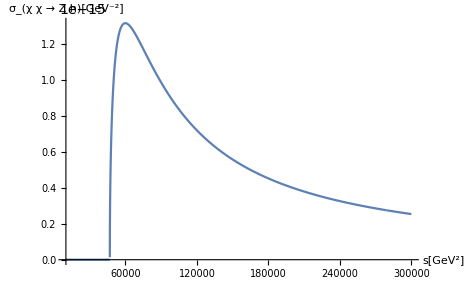
-Graphics-figure of last run

```mathematica
(*Plot[σxxZZ[10^{-3},1,1,s,10],{s,10000,300000},AxesLabel->{"s[GeV^2]","σ_(χ χ  →  Z Z)[GeV^-2]"},LabelStyle->Directive[Black,12],PlotPoints->10000] *)
```

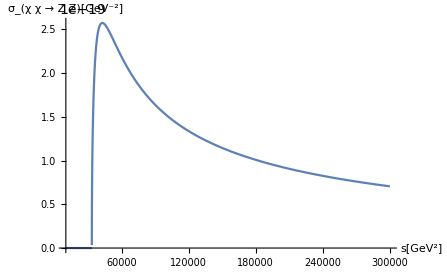
-Graphics-figure of last run

```mathematica
(*Plot[σxxWW[10^{-3},1,1,s,10],{s,10000,300000},AxesLabel->{"s[GeV^2]","σ_(χ χ  →  W W)[GeV^-2]"},LabelStyle->Directive[Black,12]] *)
```

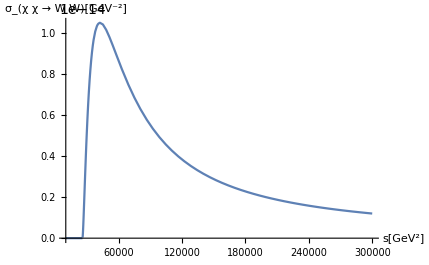
-Graphics-figure of last run

```mathematica
(*LogPlot[σxxff[10^{-3},1,1,s,10],{s,0,14000},AxesLabel->{"s[GeV^2]","σ_(χ χ  →  f f)[GeV^-2]"},LabelStyle->Directive[Black,12], PlotRange->All] *)
```

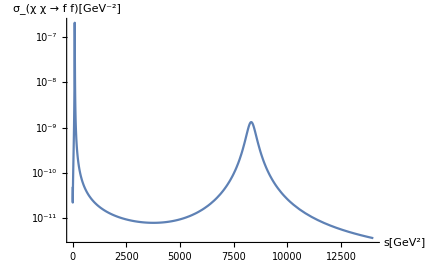
-Graphics-figure of last run

```mathematica
(*Plot[σxxZdZd[10^{-3},1,1,s,10],{s,0,4000},AxesLabel->{"s[GeV^2]","σ_(χ χ  →  SubscriptBox[Z, D]SubscriptBox[Z, D])[GeV^-2]"},LabelStyle->Directive[Black,12], PlotRange->All,PlotPoints->10000] *)
```

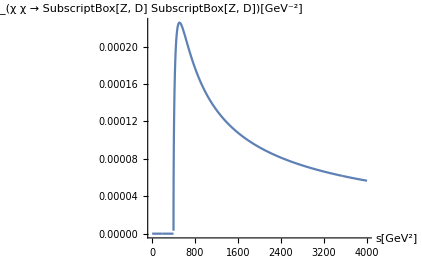
-Graphics- figure of last run

```mathematica
(*LogLogPlot[σZdZdXX[10^{-3},1,1,s,10],{s,0,4000},AxesLabel->{"s[GeV^2]","σ_Z_D[GeV^-2]"},LabelStyle->Directive[Black,12], PlotRange->All]*)
```

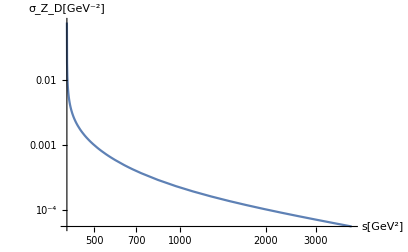
-Graphics- figure of last run

```mathematica
(*LogLogPlot[σZdZdff[10^{-3},1,1,s,10],{s,0,4000},AxesLabel->{"s[GeV^2]","σ_Z_D[GeV^-2]"},LabelStyle->Directive[Black,12], PlotRange->All]*)
```

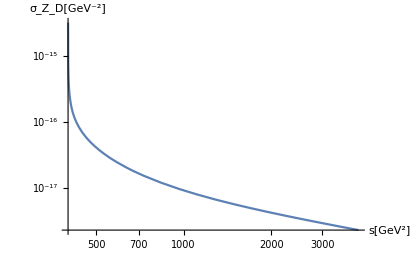
-Graphics-figure of last run

```mathematica
(*LogLogPlot[σZdfAftot[10^{-3},1,1,s,10],{s,0,4000},AxesLabel->{"s[GeV^2]","σ_Z_D[GeV^-2]"},LabelStyle->Directive[Black,12], PlotRange->All]*)
```

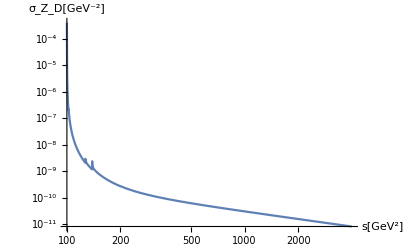
-Graphics-figure of last run

```mathematica
(*LogLogPlot[σZdAff[10^{-3},1,1,s,10],{s,0,4000},AxesLabel->{"s[GeV^2]","σ_Z_D[GeV^-2]"},LabelStyle->Directive[Black,12], PlotRange->All]*)
```

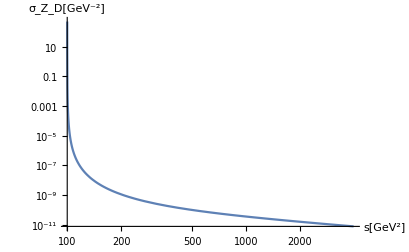
-Graphics- figure of last run

## Numerical pre-calculations

In this part we calculate useful numerical quantities that will be necesssary to properly solve the Boltzmann equation. Below, we list the related sections in the dissertation.

Degrees of freedom → see section 3.6
Equilibrium yield → see sections 3.1, 3.5 and 3.8
Thermally Averaged Cross Section (TACS) → see sections 3.8, appendix B and section 4.1
Thermally Averaged Decay Width Γ_(Z → χ χ)  →  see sections 3.8, appendix B

### Degrees of freedom

```mathematica
(*Importing the data of SM prection of degrees of freedom evolution. Data extracted from Daniel Baumann's book, with WebPlotDigitzer https://apps.automeris.io/wpd/ *)
(*dadosd = energy density d.o.f*)
(*dadoss = entropy density d.o.f*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
dadosd = Import["g_densidade.csv"];
```

```mathematica
dadoss= Import["g_s_maispontos.csv"];
```

```mathematica
(* Change of variables from gD(T[MeV]) to gD(x), for Subscript[m, χ] in GeV. *)
```

```mathematica
gDx[mx_] := Partition[Riffle[mx*10^3/dadosd[[All,1]],dadosd[[All,2]]],2]
```

```mathematica
gSx[mx_] := Partition[Riffle[mx*10^3/dadoss[[All,1]],dadoss[[All,2]]],2]
```

```mathematica
(*Summing the DM contribution to gSx and gDx smoothly*)
```

```mathematica
addgDM[{x_,y_}]:={x, y + HeavisideTheta[1-x] 4 7/8 + HeavisideTheta[x-1]HeavisideTheta[6-x](-4/5*7/8)(x-6)}
```

```mathematica
gDtable[mx_]:=Table[addgDM[gDx[mx]⟦i⟧],{i,1,Length[dadosd]}]
```

```mathematica
gStable[mx_]:=Table[addgDM[gSx[mx]⟦i⟧],{i,1,Length[dadoss]}]
```

```mathematica
gD[mx_]:=Interpolation[gDtable[mx],InterpolationOrder->1]
```

```mathematica
gS[mx_]:=Interpolation[gStable[mx],InterpolationOrder->1]
```

```mathematica
(*ListLogLogPlot[{gDx[0.020],gDtable[0.020]},Joined->True,PlotStyle->{Thick,Dashed},Frame->True,FrameLabel->{"x",""},LabelStyle->Directive[Black,12],PlotLegends->Placed[{"g_(ρ, MP)","g_(ρ, MP + ME)"},{0.85,0.75}]]*)
```

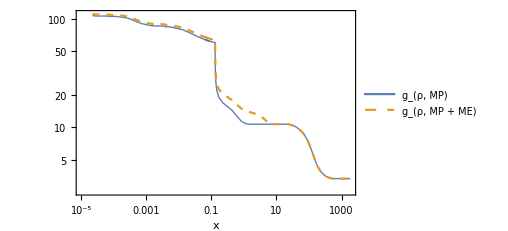
-Graphics-last run

```mathematica
(*Agora calculando (g_*)^(1/2)do G&G*)
```

```mathematica
g12[mx_,x_] := (gS[mx][x])/(√(gD[mx][x]))(1 -1/3 x/(gS[mx][x])gS[mx]'[x])
```

```mathematica
listag122[mx_] := Table[{10^lx,g12[mx,10^lx]},{lx, Log10[mx]-3., Log10[mx]+4.9, 0.05}];
```

```mathematica
g12app2[mx_] := Interpolation[listag122[mx],InterpolationOrder->1];
```

```mathematica
(*listatesteplot = g12app2[0.01]*)
```

```mathematica
(*LogLinearPlot[listatesteplot[x],{x,10^-5,10^2.9},PlotRange->All]*)
```

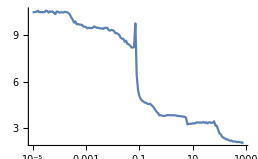
-Graphics-last run. Obs: it runs extremely faster if you run like "list = Interpolation[listag122[mx],InterpolationOrder→1];"  first, and than ask for "list[x]" than try to directly compute g12app2[mx][x]

### Equilibrium Yield

YeqF is the yield of a fermion, appart from numerical factors. For the full yield expression, we have YeqFapp.
α = E/T,  x=m/T

P.S.:  We should have keept the Maxwell-Boltzmann approximation also for the equilibrium distribution to be more consistent (See section 3.8 and Appendix B). It was realized after we generated our data. Anyway, since this DM model freezes-out at T < m_x, this shouldn’t have any appreciable effect.

```mathematica
YeqF[x_]:=NIntegrate[(α*Sqrt[(α^2-x^2)])/(E^α+1),{α,x,500.}]
```

```mathematica
YeqFtab =Table[{10^lx, YeqF[10^lx]},{lx, -4., 3., 0.005}];

Yeqpreapp = Interpolation[YeqFtab ,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
(*Yield full expression*)
```

```mathematica
YeqFapp[mx_,x_]:=(4 90)/(8 π^4 gS[mx][x])*Yeqpreapp[x]
```

```mathematica
(*LogLogPlot[{YeqF[x],Yeqpreapp[x],YeqFapp[0.01,x]},{x,0,100.}, AxesLabel->{"x","YeqF[x]"}, PlotLabel->"Equilibrium Distribution",PlotLegends->{"YeqF[x]"," Interpolation Yeqpreapp[x]","Yield YeqFapp[0.01,x]"},PlotStyle-> {Thick,Dashed}]*)
```

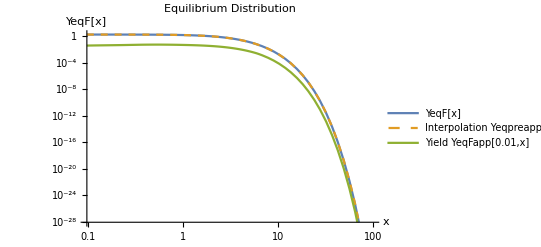
-Graphics-                                  last run

```mathematica
(*LogLogPlot[{YeqF[x],Yeqpreapp[x],YeqFapp[0.01,x]},{x,0,50}, AxesLabel->{"x","YeqF[x]"}, PlotLabel->"Equilibrium Distribution",PlotLegends->{"YeqF[x]"," Interpolation Yeqpreapp[x]","Yield YeqFapp[0.01,x]"},PlotStyle-> {Thick,Dashed},PlotRange->{Automatic,{0.01,2}}]*)
```

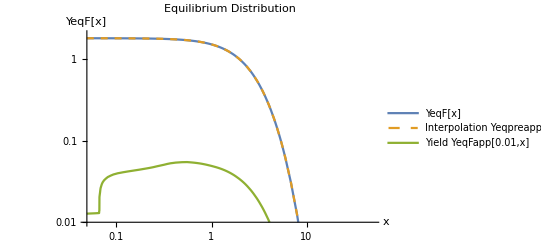
-Graphics-             Last run. Zooming in to see the jump in the yield at  T≃ 10 MeV/0.07 ≃ 150 MeV, corresponding to the decrease of gS near QCD phase transition.

### TACS Methods

```mathematica
(*TACS = Thermally Averaged Cross Section *)
```

```mathematica
(* TA212SM is the method used for Subscript[m, χ] > 20 MeV - faster and less precise *)
```

```mathematica
TA212SM[ϵ_,mx_,gD_,mzd0_,x_]:=N[ x/(8 mx^5 BesselK[2,x]^2)]NIntegrate[σSM[ϵ,mx,gD,s,mzd0](s-4 mx^2)√s BesselK[1,√s x/mx], {s, 4*mx^2, Infinity},Method->"ExtrapolatingOscillatory",PrecisionGoal->25,AccuracyGoal->20,MinRecursion->7,MaxRecursion->15]
```

```mathematica
(* TA212SM is the method used for Subscript[m, χ] ≤ 20 MeV - slower and more precise *)
(*The differences are AccuracyGoal->25 and MinRecursion->10*)
```

```mathematica
TA213SM[ϵ_,mx_,gD_,mzd0_,x_]:=N[ x/(8 mx^5 BesselK[2,x]^2)]NIntegrate[σSM[ϵ,mx,gD,s,mzd0](s-4 mx^2)√s BesselK[1,√s x/mx], {s, 4*mx^2, Infinity},Method->"ExtrapolatingOscillatory",PrecisionGoal->25,AccuracyGoal->25,MinRecursion->10,MaxRecursion->15]
```

### ⟨ Γ_(Z→χ χ) ⟩

Based on equation 5.4, to write the Boltzmann equation for DM in a simpler way, we choose to make a single list (and subsequent interpolation) of the factor (⟨Γ_(Z→ χχ)⟩ nz^eq)/s^2. We called this funcion GammaNS.

```mathematica
(*This part fixes by hand the bad behavior of Subscript[K, 1](mz/T)/Subscript[K, 2](mz/T) for small temperatures (big x = Subscript[m, x]/T values). We checked that Subscript[K, 1](mz/T)/Subscript[K, 2](mz/T) -> 1 when T -> 0 *)
```

```mathematica
fracao[mx_,x_]:= Piecewise[{{(BesselK[1,91.1876 x/mx]/BesselK[2,91.1876 x/mx]),x/mx<=8},  {1,x/mx>8}}]
```

```mathematica
{fracao[1,10],fracao[1,0.001],fracao[1,8]}
```

{1,0.0451155,0.997946}

```mathematica
(*LogLinearPlot[fracao[1,x],{x,0,50}]*)
```

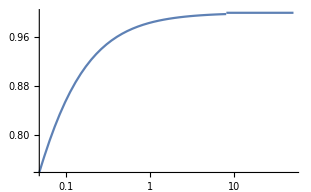
-Graphics-last run

```mathematica
(*Analytical expression for the decay width Subscript[Γ, Z -> χ χ]*)
```

```mathematica
gammaZXX [ϵ_,mx_,gD_]:=(Cosw^2 gD^2 √(1-(4 mx^2)/mz^2) (2 mx^2+mz^2) SinA^2)/(12 (Cosw^2-ϵ^2) mz π)HeavisideTheta[mz-2mx]
```

```mathematica
(* ⟨Subscript[Γ, Z -> χ χ]⟩  - see section 3.8*)
```

```mathematica
TAGamma[ϵ_,mx_,gD_,mzd0_,x_]:= Block[{mz0=91.1876,Sinw=√0.23121,Cosw=√(1-0.23121),mz=massaZ[ϵ,mzd0],SinA = Sinα[ϵ,mzd0]},

gammaZXX [ϵ,mx,gD] fracao[mx,x]]
```

```mathematica
(*LogLinearPlot[TAGamma[0.001,0.1,1,0.3,x],{x,10^-3,10^3}]*)
```

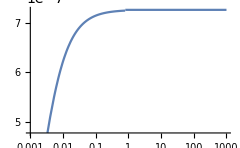
-Graphics-last run

```mathematica
(*Equilibruim Maxwell-Boltzmann distribution for the Z boson*)
```

```mathematica
NeqZ[mx_,x_]:= 3 ((mz mx)/(2 π x))^(3/2)Exp[-mz x/mx]
```

```mathematica
(*Squared entropy density - see section 3.6*)
```

```mathematica
s2[mx_,x_]:=( (2 π^2)/45(gS[mx][x] mx^3)/x^3)^2
```

```mathematica
(* Block to obtain the numerical values *)
```

```mathematica
TAGammaNS[ϵ_,mx_,gD_,mzd0_,x_]:= Block[{mz0=91.1876,Sinw=√0.23121,Cosw=√(1-0.23121),mz=massaZ[ϵ,mzd0],SinA = Sinα[ϵ,mzd0]},

gammaZXX [ϵ,mx,gD] fracao[mx,x] NeqZ[mx,x]/s2[mx,x]]
```

```mathematica
(*To make the list*)
```

```mathematica
TabGammaNS[ϵ_,mx_,gD_,mzd0_]:= ParallelTable[Quiet[{10^lx,TAGammaNS[ϵ,mx,gD,mzd0,10^lx]}],{lx,-4.,3.,0.05}]
```

```mathematica
(*testeTabGammaNS = Interpolation[TabGammaNS[0.001,0.1,1,0.3],InterpolationOrder->1]*)
```

```mathematica
(*LogLogPlot[testeTabGammaNS [x],{x,0.0001,10},PlotRange->{{0.0001,10},{10^(-100),0.1}}]*)
```

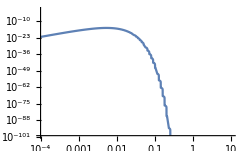
-Graphics-last run

## Scanning the parameter space

See section 4.3

#### Scan Function for m_χ>20 MeV - TA212

```mathematica
(* To scan the parameter space, we just need to specify:
  - ϵAlpha: estimate for ϵ_0,0
   - range of mx scanned: from massaInicial to massaFinal
- coupling between the DM and the DP, gD
   - the hierarchy h
   - initial and final x points to solve the Boltzmann equations: xI e xF
- step to calculate the TACS interpolation: passoTACS    
and call  VariaMassaLog (last function in this section)  *)
```

```mathematica
(*This function returns, for a given mx, the yield that corresponds to the observed abundance, Subscript[Ω, C] = 0.120*)
```

```mathematica
Y0[mx_] := Block[{gS0 = 3.94 (*Baumann, Figure 3.4*),T0 = 2.348 × 10^-4 (*in eV; Dodelson*),ρcr= 8.098×10^-11 h^2(*in eV^4,Dodelson*),Ωc = 0.120 h^-2 (*PDG*),s0 = (2 π^2)/45 gS0 T0^3},(ρcr*Ωc 10^-9)/(s0 mx)]
```

```mathematica
(*This part of the algorithm is responsible for: 
- calculate ⟨σv⟩ and ⟨Γ⟩;
 - solve the Boltzmann equation;
 - estimate Subscript[Y, ∞] = yF[xF] (the relic abundance)*)
```

```mathematica
CalculaY[ϵ_,mx_,gD_,mzd_,xI_,xF_, passoTACS_]:=

Module[{mzd0 = massalagrangiana[mzd,ϵ],TAtab212SM,TAapp212SM,TAGammaNSapp,BoltzmannSolution},

TAtab212SM= ParallelTable[Quiet[{10^lx, TA212SM[ϵ,mx,gD,mzd0,10^lx]}], {lx, Log10[xI],  Log10[xF]+passoTACS,passoTACS}];

TAapp212SM= Interpolation[TAtab212SM,InterpolationOrder->1];

TAGammaNSapp = Interpolation[TabGammaNS[ϵ,mx,gD,mzd0],InterpolationOrder->1];

BoltzmannSolution = NDSolve[{yF'[x]==(- √((π (1.221*10^19)^2)/45) (g12appmx[x]*mx)/(2*x^2))(TAapp212SM[x]*(yF[x]^2-YeqFappmx[x]^2)+TAGammaNSapp[x]/YeqFappmx[x]^2*(yF[x]^2-YeqFappmx[x]^2)) , yF[xI]==YeqFappmx[xI]}, yF, {x,xI,xF},Method->{"StiffnessSwitching",Method-> {"ExplicitRungeKutta",Automatic}},AccuracyGoal->13, PrecisionGoal->13];
(yF[xF]/.BoltzmannSolution)⟦1⟧]
```

```mathematica
(* WHEN Subscript[Y, ∞]_n,0 > Y0,  this part of the algorithm is responsible for: 
- select the ϵ values that will be tested (ϵ = 10^k);
  - save the obtained "vectors" (ϵ_n,i, mx_n, Subscript[Y, ∞]_n,i) for different values of ϵ tested, fixed h, Subscript[g, D] and mx_n
 - save the best estimate for ϵ_(n+1,0) *)
```

```mathematica
Olheparacima[ϵanterior_,mx_,gD_,h_,xI_,xF_,passoTACS_]:=Module[{k=Log10[ϵanterior](*+0.1*),a= Y0[mx],lista={}},
While[a≥ Y0[mx],(*Print[10^K];*)a=CalculaY[10^k,mx,gD,h mx,xI,xF,passoTACS];
lista = Append[lista,{10^k,mx,a}];
k=k+0.02
]  ;
melhorϵ=lista⟦Position[Abs[(lista[[All,3]]-Y0[mx])/Y0[mx]],Min[Abs[(lista[[All,3]]-Y0[mx])/Y0[mx]]]]⟦1,1⟧,1⟧;
{melhorϵ,lista}
]
```

```mathematica
(* WHEN Subscript[Y, ∞]_n,0 < Y0,  this part of the algorithm is responsible for: 
- select the ϵ values that will be tested (ϵ = 10^k);
  - save the obtained "vectors" (ϵ_n,i, mx_n, Subscript[Y, ∞]_n,i) for different values of ϵ tested, fixed h, Subscript[g, D] and mx_n
 - save the best estimate for ϵ_(n+1,0) *)
```

```mathematica
Olheparabaixo[ϵanterior_,mx_,gD_,h_,xI_,xF_,passoTACS_]:=Module[{k=Log10[ϵanterior](*-0.1*),a= Y0[mx],lista={}},
While[a≤  Y0[mx],(*Print[10^k];*)a=CalculaY[10^k,mx,gD,h mx,xI,xF,passoTACS];
lista = Append[lista,{10^k,mx,a}];
k=k-0.02
]  ;
(*lista = Append[lista,{10^-5.1,mx,CalculaY[10^-5.1,mx,gD,h mx,xI,xF,passoTACS]}];
lista = Append[lista,{10^-2.4,mx,CalculaY[10^-2.4,mx,gD,h mx,xI,xF,passoTACS]}];*)
melhorϵ=lista⟦Position[Abs[(lista[[All,3]]-Y0[mx])/Y0[mx]],Min[Abs[(lista[[All,3]]-Y0[mx])/Y0[mx]]]]⟦1,1⟧,1⟧;
{melhorϵ,lista}
]
```

```mathematica
(*This part of the algorithm is responsible for: 
- calculate Subscript[Y, ∞] (ϵ_n,0 , mx_n);
  - compare with Y0;
  - choose using Olheparacima or Olheparabaixo *)
```

```mathematica
DirecaoVarrer[ϵanterior_,mx_,gD_,h_,xI_,xF_,passoTACS_]:= Module[{Ycalculado =CalculaY[ϵanterior,mx,gD,h mx,xI,xF,passoTACS]},
Piecewise[{{Olheparacima[ϵanterior,mx,gD,h,xI,xF,passoTACS],Ycalculado>Y0[mx]},{Olheparabaixo[ϵanterior,mx,gD,h,xI,xF,passoTACS],Ycalculado≤Y0[mx]}}]]
```

```mathematica
(*VariaMassaLog is the main function of the algorithm
 - select the mx values, and for each mx: 
    - calculate gSmx, YeqFappmx, g12appmx for each selected mx (these quantities are only mx dependent)
     - calls DirecaoVarrer[ϵ_(n,0) , mx_n, gD, h, xI, xF, passoTACS]
     - save the data from mx_n on the main list (ListaPrincipal), that contains all data
     - sets ϵ_(n+1,0)
 - after scanning exports a big list that contains all (ϵ_{n,i} , mx_n, Subscript[Y, ∞]_{n,i}) calculated *)
```

```mathematica
VariaMassaLog[ϵAlpha_,massaInicial_,massaFinal_,gD_,h_,xI_,xF_,passoTACS_]:= Module[{ϵanterior = ϵAlpha,ListaPrincipal={}},

Do[mx=10^lm;

gSmx = gS[mx];

YeqFappmx[x_]:= (4 90)/(8 π^4 gSmx[x])*Yeqpreapp[x];

g12appmx = Interpolation[listag122[mx],InterpolationOrder->1];

A = DirecaoVarrer[ϵanterior,mx,gD,h,xI,xF,passoTACS];

ListaPrincipal=Append[ListaPrincipal,A⟦2⟧];

ϵanterior=A⟦1⟧,

{lm,Log10[massaInicial],Log10[massaFinal]+0.023,0.023}];

ListaPrincipal]
```

#### Scan Function for m_χ≲20 MeV - TA213

```mathematica
(*Completely analogous to TA212 - see coments above*)
```

```mathematica
Y0[mx_] := Block[{gS0 = 3.94 (*Baumann, Figure 3.4*),T0 = 2.348 × 10^-4 (*in eV; Dodelson*),ρcr= 8.098×10^-11 h^2(*in eV^4,Dodelson*),Ωc = 0.120 h^-2 (*Dodelson e PDG*),s0 = (2 π^2)/45 gS0 T0^3},(ρcr*Ωc 10^-9)/(s0 mx)]
```

```mathematica
CalculaY213[ϵ_,mx_,gD_,mzd_,xI_,xF_, passoTACS_]:=

Module[{mzd0 = massalagrangiana[mzd,ϵ],TAtab212SM,TAapp212SM,TAGammaNSapp,BoltzmannSolution},

TAtab212SM= ParallelTable[Quiet[{10^lx, TA213SM[ϵ,mx,gD,mzd0,10^lx]}], {lx, Log10[xI],  Log10[xF]+passoTACS,passoTACS}];

TAapp212SM= Interpolation[TAtab212SM,InterpolationOrder->1];

TAGammaNSapp = Interpolation[TabGammaNS[ϵ,mx,gD,mzd0],InterpolationOrder->1];

BoltzmannSolution = NDSolve[{yF'[x]==(- √((π (1.221*10^19)^2)/45) (g12appmx[x]*mx)/(2*x^2))(TAapp212SM[x]*(yF[x]^2-YeqFappmx[x]^2)+TAGammaNSapp[x]/YeqFappmx[x]^2*(yF[x]^2-YeqFappmx[x]^2)) , yF[xI]==YeqFappmx[xI]}, yF, {x,xI,xF},Method->{"StiffnessSwitching",Method-> {"ExplicitRungeKutta",Automatic}},AccuracyGoal->13, PrecisionGoal->13];
(yF[xF]/.BoltzmannSolution)⟦1⟧]
```

```mathematica
Olheparacima213[ϵanterior_,mx_,gD_,h_,xI_,xF_,passoTACS_]:=Module[{k=Log10[ϵanterior](*+0.1*),a= Y0[mx],lista={}},
While[a≥ Y0[mx],a=CalculaY213[10^k,mx,gD,h mx,xI,xF,passoTACS];
lista = Append[lista,{10^k,mx,a}];
k=k+0.04
]  ;

melhorϵ=lista⟦Position[Abs[(lista[[All,3]]-Y0[mx])/Y0[mx]],Min[Abs[(lista[[All,3]]-Y0[mx])/Y0[mx]]]]⟦1,1⟧,1⟧;
{melhorϵ,lista}
]
```

```mathematica
Olheparabaixo213[ϵanterior_,mx_,gD_,h_,xI_,xF_,passoTACS_]:=Module[{k=Log10[ϵanterior](*-0.1*),a= Y0[mx],lista={}},
While[a≤  Y0[mx],(*Print[10^k];*)a=CalculaY213[10^k,mx,gD,h mx,xI,xF,passoTACS];
lista = Append[lista,{10^k,mx,a}];
k=k-0.04
]  ;

melhorϵ=lista⟦Position[Abs[(lista[[All,3]]-Y0[mx])/Y0[mx]],Min[Abs[(lista[[All,3]]-Y0[mx])/Y0[mx]]]]⟦1,1⟧,1⟧;
{melhorϵ,lista}
]
```

```mathematica
DirecaoVarrer213[ϵanterior_,mx_,gD_,h_,xI_,xF_,passoTACS_]:= Module[{Ycalculado =CalculaY213[ϵanterior,mx,gD,h mx,xI,xF,passoTACS]},

Piecewise[{{Olheparacima213[ϵanterior,mx,gD,h,xI,xF,passoTACS],Ycalculado>Y0[mx]},{Olheparabaixo213[ϵanterior,mx,gD,h,xI,xF,passoTACS],Ycalculado≤Y0[mx]}}]]
```

```mathematica
VariaMassaLog213[ϵAlpha_,massaInicial_,massaFinal_,gD_,h_,xI_,xF_,passoTACS_]:= Module[{ϵanterior = ϵAlpha,ListaPrincipal={}},

Do[mx=10^lm;

gSmx = gS[mx];

YeqFappmx[x_]:= (4 90)/(8 π^4 gSmx[x])*Yeqpreapp[x];

g12appmx = Interpolation[listag122[mx],InterpolationOrder->1];

A = DirecaoVarrer213[ϵanterior,mx,gD,h,xI,xF,passoTACS];

ListaPrincipal=Append[ListaPrincipal,A⟦2⟧];

ϵanterior=A⟦1⟧,

{lm,Log10[massaInicial],Log10[massaFinal]+0.05,0.05}];

ListaPrincipal]
```

#### Example: obtaining and visualizing data

```mathematica
(* To scan the parameter space, we just need to specify:
  - ϵAlpha: estimate for ϵ_0,0
   - range of mx scanned: from massaInicial to massaFinal
- coupling between the DM and the DP, gD
   - the hierarchy h
   - initial and final x points to solve the Boltzmann equations: xI e xF
- step to calculate the TACS interpolation: passoTACS    
and call  VariaMassaLog   *)
```

```mathematica
(*here an small example: ϵAlpha = 0.018, mx from 400 to 500 MeV, gD=1, h=13, xI=1, xF=200, passoTACS = 0.1 *)
```

```mathematica
(*AbsoluteTiming[Export["testingdata.m",VariaMassaLog[0.018,0.4,0.5,1,13,1,200,0.1]]]*)
```

{2467.75, "testingdata.m"} ------------------> Last run. Yes, it takes  some time to run.

```mathematica
(*To avoid losing data, we export it  after each scan. After that, we import the data to treat it. (This test .m file is also available here in the github folder)*)
(*The structure of the data is {    {{mx_0, ϵ_0,0, Y_0,0},{mx_0, ϵ_0,1, Y_0,1},...,{mx_0, ϵ_0,i, Y_0,i}},             ....,  {{mx_n, ϵ_n,0, Y_n,0},{mx_n, ϵ_n,1, Y_n,1},...,} ,.....         }*)
SetDirectory[NotebookDirectory[]];
datatest = Import["testingdata.m"]
```

{{{0.018,0.4,1.07222×10^-9},{0.0171899,0.4,1.16938×10^-9}},{{0.018,0.421755,1.1227×10^-9},{0.0188483,0.421755,1.02947×10^-9}},{{0.0188483,0.444693,1.07726×10^-9},{0.0197366,0.444693,9.87837×10^-10},{0.0206668,0.444693,9.05804×10^-10}},{{0.0197366,0.468878,1.03306×10^-9},{0.0206668,0.468878,9.47339×10^-10},{0.0216408,0.468878,8.68705×10^-10}},{{0.0206668,0.494379,9.8996×10^-10},{0.0216408,0.494379,9.07858×10^-10},{0.0226607,0.494379,8.32542×10^-10}},{{0.0216408,0.521267,9.47916×10^-10},{0.0226607,0.521267,8.69348×10^-10},{0.0237286,0.521267,7.97263×10^-10}}}

```mathematica
(*With this complete data, we use the function Fazparesmedio to finally estimate the pairs (mx_n, ϵ_n), that reproduce the observed relic abundance (as explained in section 4.3). *)
```

```mathematica
Fazparesmedio[Listona_]:=Module[{listaparesmedio={}},

Do[lista  =  Listona⟦i⟧;
mx = lista⟦1,2⟧;

ϵmedio =( lista⟦-2,1⟧ + lista⟦-1,1⟧)/2;

listaparesmedio = Append[listaparesmedio,{mx,ϵmedio}],
{i,1,Length[Listona]}];
listaparesmedio]
```

```mathematica
Fazparesmedio[datatest]
```

{{0.4,0.0175949},{0.421755,0.0184242},{0.444693,0.0202017},{0.468878,0.0211538},{0.494379,0.0221507},{0.521267,0.0231946}}

```mathematica
(*Visualizing the data*)
```

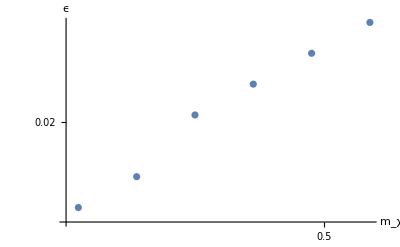

```mathematica
ListLogLogPlot[Fazparesmedio[datatest],AxesLabel->{"m_χ","ϵ"},LabelStyle->Directive[Black,12]]
```